```mathematica
Define symmetric quantization rho
```

```mathematica
CleanSlate;
$MinPrecision=MachinePrecision;
  ρz[z_] := z/(1 + Sqrt[1 - z])^2; 
 ρzb[z_] := ρz[Conjugate[z]]; 
 (*error estimates*)
    ρintErrorEstimateG[d_, DDs_, z_, γ_] := (2^(γ + 4*d)*β^(γ - 4*d)*Gamma[1 - γ + 4*d, β*DDs])/(Gamma[1 - γ + 4*d]*(1 - r^2)^γ)/.  {r -> Abs[ρz[z]], β -> -Log[Abs[ρz[z]]]}; 
      ρintErrorEstimateFt[d_, DDs_, z_, γ_] := 
     v^d*ρintErrorEstimateG[d, DDs, z, γ] + u^d*ρintErrorEstimateG[d, DDs, 1 - z, γ] /. {u -> z*Conjugate[z], v -> (1 - z)*(1 - Conjugate[z])}; 
     (*coefficients and prefactors*)
    kfunctAna[β_, x_] := Exp[(β/2)*Log[4*((1 - Sqrt[1 - x])^2/x)]]*(x/(2*(1 - x)^(1/4)*(1 - Sqrt[1 - x]))); 
    ConformalBlockAna[DD_, l_, z_] := ((-1)^l/2^l)*((z*Conjugate[z])/(z - Conjugate[z]))*(kfunctAna[DD + l, z]*kfunctAna[DD - l - 2, Conjugate[z]] - 
       kfunctAna[DD + l, Conjugate[z]]*kfunctAna[DD - l - 2, z]);
       (*derivatives*)
       FAnaDer[DD_, l_, z_] := (1/(z - Conjugate[z]))*(-1)^(2*l)*(1 - z)*z*
      (1 - Conjugate[z])*Conjugate[z]*(-((2^(-5 + 2*DD)*((1 - Sqrt[z])/(1 + Sqrt[z]))^((1/2)*(-2*l + DD))*(1 - z)*
          ((1 - Sqrt[Conjugate[z]])/(1 + Sqrt[Conjugate[z]]))^((1/2)*(-2*l + DD))*(-((1 - Sqrt[z])/(1 + Sqrt[z]))^(2*l) - 
           Sqrt[z]*(((1 - Sqrt[z])/(1 + Sqrt[z]))^(2*l) + ((1 - Sqrt[Conjugate[z]])/(1 + Sqrt[Conjugate[z]]))^(2*l)) + 
           ((1 - Sqrt[Conjugate[z]])/(1 + Sqrt[Conjugate[z]]))^(2*l) + (((1 - Sqrt[z])/(1 + Sqrt[z]))^(2*l) + 
             Sqrt[z]*(((1 - Sqrt[z])/(1 + Sqrt[z]))^(2*l) - ((1 - Sqrt[Conjugate[z]])/(1 + Sqrt[Conjugate[z]]))^(2*l)) + 
             ((1 - Sqrt[Conjugate[z]])/(1 + Sqrt[Conjugate[z]]))^(2*l))*Sqrt[Conjugate[z]])*(1 - Conjugate[z])*
          (Log[16] + Log[-((-1 + Sqrt[z])/(1 + Sqrt[z]))] + Log[-((-1 + Sqrt[Conjugate[z]])/(1 + Sqrt[Conjugate[z]]))]))/
         ((-1 + Sqrt[z])^2*z^(1/4)*(-1 + Sqrt[Conjugate[z]])^2*Conjugate[z]^(1/4))) + (2^(-5 + 2*DD)*((-1 + Sqrt[1 - z])^2/z)^((1/2)*(-2*l + DD))*z*
         ((-1 + Sqrt[1 - Conjugate[z]])^2/Conjugate[z])^((1/2)*(-2*l + DD))*Conjugate[z]*(-2*z*(-((-2 + 2*Sqrt[1 - z] + z)/z))^(2*l)*
           (-1 + Sqrt[1 - Conjugate[z]]) + Conjugate[z]*(2*(-1 + Sqrt[1 - z])*(-((-2 + 2*Sqrt[1 - Conjugate[z]] + Conjugate[z])/Conjugate[z]))^(2*l) + 
            z*(-(-((-2 + 2*Sqrt[1 - z] + z)/z))^(2*l) + (-((-2 + 2*Sqrt[1 - Conjugate[z]] + Conjugate[z])/Conjugate[z]))^(2*l))))*
         (Log[16] + Log[(-1 + Sqrt[1 - z])^2/z] + Log[(-1 + Sqrt[1 - Conjugate[z]])^2/Conjugate[z]]))/((-1 + Sqrt[1 - z])^3*(1 - z)^(1/4)*
         (-1 + Sqrt[1 - Conjugate[z]])^3*(1 - Conjugate[z])^(1/4))); 
	 ConformalBlockAnaDer[DD_, l_, z_] := 
     -((I*(-1)^l*2^(-6 - l + 2*DD)*((-1 + Sqrt[1 - z])^2/z)^((1/2)*(-l + DD))*Abs[z]^4*((-1 + Sqrt[1 - Conjugate[z]])^2/Conjugate[z])^
         ((1/2)*(-l + DD))*(2*z*(-1 + Sqrt[1 - Conjugate[z]])*(-((-2 + 2*Sqrt[1 - Conjugate[z]] + Conjugate[z])/Conjugate[z]))^l + 
         Conjugate[z]*(-2*(-1 + Sqrt[1 - z])*(-((-2 + 2*Sqrt[1 - z] + z)/z))^l + z*(-(-((-2 + 2*Sqrt[1 - z] + z)/z))^l + 
             (-((-2 + 2*Sqrt[1 - Conjugate[z]] + Conjugate[z])/Conjugate[z]))^l)))*(Log[(16*(-1 + Sqrt[1 - z])^2)/z] + 
         Log[(-1 + Sqrt[1 - Conjugate[z]])^2/Conjugate[z]]))/((-1 + Sqrt[1 - z])^3*(1 - z)^(1/4)*(-1 + Sqrt[1 - Conjugate[z]])^3*
        (1 - Conjugate[z])^(1/4)*Im[z])); 
	kfunct[β_, x_] := kfunct[β, x] = x^(β/2)*Hypergeometric2F1[β/2, β/2, β, x]; 
    ConformalBlock[DD_, l_, z_] := ((-1)^l/2^l)*((z*Conjugate[z])/(z - Conjugate[z]))*(kfunct[DD + l, z]*kfunct[DD - l - 2, Conjugate[z]] - 
       kfunct[DD + l, Conjugate[z]]*kfunct[DD - l - 2, z]); 
      
      (*random sample of z around (1/2+I0)*)
           Sample[nz_,var_,seed_] := Module[{imax}, SeedRandom[seed];Table[Abs[RandomVariate[NormalDistribution[0, var]]]+
           1/2+I Abs[RandomVariate[NormalDistribution[0, var]]],{imax,1,nz}]]; 
(*Exponential factor to renormalize*)
dimExpFactor[a_,b_]:=Log[4(1-Sqrt[1/2 -a -b])^2/(1/2 + a +b)];

renomFactor[dim_]:=Exp[-(dim-1)dimExpFactor[0,0]];
(*renomFactor[dim_]:=1;*)
(*Conformal Blocks*)
qQGen[Δϕ_,Δ_,L_,zsample_]:=renomFactor[Δ] (((1 - zsample)*(1 - Conjugate[zsample]))^Δϕ    ConformalBlock[Δ, L , zsample]- ((zsample)*( Conjugate[zsample]))^Δϕ ConformalBlock[Δ, L,1- zsample])2^(L);
qQGenDims[Δϕ_,ΔL_,z_]:=qQGen[1,#1[[1]],#1[[2]], z]&/@ΔL
MetroGoFixedSelectiveDir[Δϕ_,ΔLOriginal_,Ndit_,prec_,betad_,seed_,sigmaMC_,dcross_,lmax_,idTag_,initialOps_]:=Block[{itd, DDldata, sigmaz, sigmaD, Action=100000000, Actionnew=0, Action0, DDldatafixed, QQ0, QQ1, str, Lmax, Nvmax, rr, metcheck, sigmaDini, 
    zsample, Idsample, Nz, PP0, PP1, lr, nr, Errvect, Factor, Factor0, ppm, DDldataEx, PPEx, QQEx, Idsampleold, ip, nvmax, QQFold,  
    IdsampleEx,zOPE,QQOPE,Calc,coeffTemp,Ident,OPEcoeff,ActionTot,  TotD ,DDldataold,QQold,ΔLOld,dimToVary,PP,QQsave,ΔL,dw,smearedaction}, 
    (*precision*)
SetOptions[{RandomReal,RandomVariate},WorkingPrecision->prec];
$MaxPrecision=prec;
$MinPrecision=prec;

    SeedRandom[seed];
    Nz=Length[ΔLOriginal]+1;
  zsample = Sample[Nz,1/100,seed]; 
Idsample = SetPrecision[Table[(zsample[[zv]]*Conjugate[zsample[[zv]]])^Δϕ -
        ((1 - zsample[[zv]])*(1 - Conjugate[zsample[[zv]]]))^Δϕ, {zv, 1, Nz}],prec];
    ΔL = ΔLOriginal;
  ΔL[[All,1]] = SetPrecision[ΔL[[All,1]],prec];
  

    QQ0 = qQGenDims[Δϕ,ΔL,zsample];
     
    (*Monte Carlo Iteration*)
TotD =   Reap[ Do[
$MinPrecision=prec;
          ΔLOld=ΔL;
          QQold=QQ0;  

(*let every successive run start by varying only the new operator*)
        If[it<Ndit/10&& Nz!=initialOps+1,dimToVary=Nz-1,  dimToVary = RandomInteger[{1,lmax}]];
       (*Shift one dimension by a random amount*)       
          ΔL[[dimToVary,1]] = ΔL[[dimToVary,1]]+ RandomVariate[NormalDistribution[0, sigmaMC]];
(*Reevaluate coefficients*)
           QQ0[[dimToVary]] = qQGen[Δϕ,ΔL[[dimToVary]][[1]],ΔL[[dimToVary]][[2]],zsample];
          
    (*Coefficients for LES and action thence*)
          PP = Join[QQ0, {Idsample}]; 
          Actionnew = Log[Det[PP]^2]; 
QQsave=QQ0;
(*Brot noch schmieren? *)
smearedaction=Reap[Table[
           QQ0[[dimToVary]] =qQGen[Δϕ,ΔL[[dimToVary]][[1]]+dcross,ΔL[[dimToVary]][[2]],zsample];  PP = Join[QQ0, {Idsample}]; 
          Sow[ Log[Det[PP]^2]];
           QQ0[[dimToVary]] =qQGen[Δϕ,ΔL[[dimToVary]][[1]]-dcross,ΔL[[dimToVary]][[2]],zsample];  PP = Join[QQ0, {Idsample}]; 
          Sow[ Log[Det[PP]^2]];QQ0=QQsave;,{dimToVary,1,lmax}]];

 Actionnew =Actionnew +Total[smearedaction[[2]]//Flatten] ;
         

          metcheck = Exp[(-betad)*(Actionnew - Action)];
          rr = RandomReal[{0, 1}];
          If[metcheck>rr, Action = Actionnew,ΔL=ΔLOld;QQ0=QQold];
          
$MinPrecision=10;
   dw=ΔL[[All,1]];
          Sow[ {it, dw, N[Action,10]}],
     {it, 1, Ndit}]]; 
$MinPrecision=3;
      Export["Res-fixed_Param_Nit="<>ToString[Ndit]<>"prec="<>ToString[prec]<>"beta="<>ToString[N[betad,3]]<>"sigmaMC="<>ToString[N[sigmaMC,3]]<>"dcross="<>ToString[N[dcross,3]]<>"seed="<>ToString[seed]<>"id="<>idTag<>".txt", TotD[[2]]];]

weightedLeastSquares[qq0_,id_,w_]:=Block[{rhovec,nu,s,r},
rhovec=Inverse[Transpose[qq0].w.qq0].Transpose[qq0] . w.id;
nu = Dimensions[w][[1]]-Length[rhovec];
r=(qq0.rhovec-id);
s=r.w.r;
Return[{rhovec,(Diagonal[Inverse[Transpose[qq0].w.qq0]])^(-1/2), s/nu}]];

metroReturnAvg[prec_,nit_,β_,ΔL_,seed_,initialOps_,idtag_]:=Block[{data},
MetroGoFixedSelectiveDir[1,ΔL,nit,prec,β,seed,1/10,1/3,Length[ΔL],ToString[Length[ΔL]]<>"id"<>idtag,initialOps];
data= Get["Res-fixed_Param_Nit="<>ToString[nit]<>"prec="<>ToString[prec]<>"beta="<>ToString[N[β,3]]<>"sigmaMC="<>ToString[N[1/10,3]]<>"dcross="<>ToString[N[1/3,3]]<>"seed="<>ToString[seed]<>"id="<>ToString[Length[ΔL]]<>"id"<>idtag<>".txt"];
Export["Plot-fixed_Param_Nit="<>ToString[nit]<>"prec="<>ToString[prec]<>"beta="<>ToString[N[β,3]]<>"sigmaMC="<>ToString[N[1/10,3]]<>"dcross="<>ToString[N[1/3,3]]<>"seed="<>ToString[seed]<>"id="<>ToString[Length[ΔL]]<>"id"<>idtag<>".pdf",ListPlot[Table[data[[All,2]][[All,i]],{i,1,Length[ΔL]}],Joined->True,GridLines->Automatic,PlotStyle->Thin,PlotLabel->ToString[Length[ΔL]]<>"id"<>idtag<>"Nit="<>ToString[nit]<>" prec="<>ToString[prec]<>" beta="<>ToString[N[β,3]]<>" sigmaMC="<>ToString[N[1/10,3]]<>" dcross="<>ToString[N[1/3,3]]<>"seed="<>ToString[seed]]];
Export["zoom-Plot-fixed_Param_Nit="<>ToString[nit]<>"prec="<>ToString[prec]<>"beta="<>ToString[N[β,3]]<>"sigmaMC="<>ToString[N[1/10,3]]<>"dcross="<>ToString[N[1/3,3]]<>"seed="<>ToString[seed]<>"id="<>ToString[Length[ΔL]]<>"id"<>idtag<>".pdf",ListPlot[Table[data[[All,2]][[All,i]]-2i+1,{i,1,Length[ΔL]}],Joined->True,GridLines->Automatic,PlotStyle->Thin,PlotRange->{{0,nit},{0,2}},PlotLabel->ToString[Length[ΔL]]<>"id"<>idtag<>"Nit="<>ToString[nit]<>" prec="<>ToString[prec]<>" beta="<>ToString[N[β,3]]<>" sigmaMC="<>ToString[N[1/10,3]]<>" dcross="<>ToString[N[1/3,3]]<>"seed="<>ToString[seed]]];
{Mean[data[[All,2]][[nit-100;;nit,1;;Length[ΔL]]]],StandardDeviation[data[[All,2]][[nit-100;;nit,1;;Length[ΔL]]]]}]

checkMetroWeighted[Δϕ_,ΔLOriginal_,prec_,seed_,Nz_,sigmaz_]:=Block[{itd, DDldata,  sigmaD, Action=100000000, Actionnew=0, Action0, DDldatafixed, QQ0, QQ1, str, Lmax, Nvmax, rr, metcheck, sigmaDini, 
    zsample, Idsample, PP0, PP1, lr, nr, Errvect, Factor, Factor0, ppm, DDldataEx, PPEx, QQEx, Idsampleold, ip, nvmax, QQFold,  
    ΔLOld,dimToVary,PP,QQsave,ΔL=ΔLOriginal,dw,smearedaction,ρ,rhovec,eqs,rhosol,last,check,results,indices,rhopos,meanrho,sigmarho,finalcheck,errSample}, 
    (*precision*)
SetOptions[{RandomReal,RandomVariate,NSolve},WorkingPrecision->prec];
$MaxPrecision=prec;
$MinPrecision=prec;

    SeedRandom[seed];
  zsample = Sample[Nz,sigmaz,seed]; 
Idsample = SetPrecision[Table[(zsample[[zv]]*Conjugate[zsample[[zv]]])^Δϕ -
        ((1 - zsample[[zv]])*(1 - Conjugate[zsample[[zv]]]))^Δϕ, {zv, 1, Nz}],prec];
    ΔL = ΔLOriginal;
  ΔL[[All,1]] = SetPrecision[ΔL[[All,1]],prec];
  

    QQ0 = qQGenDims[Δϕ,ΔL,zsample];
errSample=Table[ ρintErrorEstimateFt[Δϕ,ΔLOriginal[[-1,1]],zsample[[i]],1],{i,1,Nz}];
results=weightedLeastSquares[(QQ0//Transpose),Idsample,DiagonalMatrix[errSample^(-2)]];
finalcheck=Abs[results[[1]].QQ0-Idsample]<errSample//Thread;
Return[{results,And@@finalcheck}];
]
mcIterator[initialOps_,finalOps_,ΔLinitial_,β_,nz_,prec_,seed_,nits_,runid_]:=Block[{ΔL=ΔLinitial,results},
results=Reap[Table[ΔL[[1;;it,1]]=Sow[metroReturnAvg[prec,nits[[it-initialOps+1]],β[[it-initialOps+1]],ΔL[[1;;it]],seed,initialOps,runid]][[1]];
Sow[checkMetroWeighted[1,ΔL[[1;;it]],prec,seed,nz,runid]];
,{it,initialOps,finalOps}]];
Export["averages_n_checks"<>"from"<>ToString[initialOps]<>"to"<>ToString[finalOps]<>runid<>"prec="<>ToString[prec]<>"seed="<>ToString[seed]<>"nz="<>ToString[nz]<>".txt", results];
]
mcPlotDimsAndOPEs[initialOps_,finalOps_,nz_,prec_,seed_,runid_]:=Block[{data,dims,opes,mcDims,mcOpes,refDims,refOpes,nrecs=(finalOps-initialOps) +1},
data= Get["averages_n_checks"<>"from"<>ToString[initialOps]<>"to"<>ToString[finalOps]<>runid<>"prec="<>ToString[prec]<>"seed="<>ToString[seed]<>"nz="<>ToString[nz]<>".txt"];
dims=data[[1,Range[1,2nrecs -1,2]]];
opes=data[[1,Range[2,2nrecs ,2]]];
mcDims=ListPlot[dims[[;;,1,1;;4]]//Transpose,PlotLegends->{"l=0","l=2","l=4","l=6"},PlotRange->All];
refDims=Plot[{2,4,6,8},{x,0,nrecs},PlotStyle->Dashed];
mcOpes=ListPlot[opes[[;;,1,1,1;;4]]//Transpose,PlotLegends->{"l=0","l=2","l=4","l=6"},PlotRange->All];
refOpes=Plot[{2,1/3},{x,0,nrecs},PlotStyle->Dashed];
Export["dims-plot"<>"from"<>ToString[initialOps]<>"to"<>ToString[finalOps]<>runid<>"prec="<>ToString[prec]<>"seed="<>ToString[seed]<>"nz="<>ToString[nz]<>".pdf",Show[mcDims,refDims],PlotLabel->"Dims_from"<>ToString[initialOps]<>"to"<>ToString[finalOps]<>runid<>"prec="<>ToString[prec]<>"seed="<>ToString[seed]];
Export["opes-plot"<>"from"<>ToString[initialOps]<>"to"<>ToString[finalOps]<>runid<>"prec="<>ToString[prec]<>"seed="<>ToString[seed]<>"nz="<>ToString[nz]<>".pdf",Show[mcOpes,refOpes],PlotLabel->"OPEs_from"<>ToString[initialOps]<>"to"<>ToString[finalOps]<>runid<>"prec="<>ToString[prec]<>"seed="<>ToString[seed]];
Return[opes[[;;,2]]]
]
deltaFree[n_]:={2#,2#-2}&/@Range[1,n,1];
opeFreeRen[n_]:=(renomFactor[2#])^(-1) 2((2#-2)!)^2/(2(2#-2))!&/@Range[1,n,1];
(*deltascanner*)
checkMetroWScan[Δϕ_,ΔLOriginal_,prec_,seed_,nZ_,sigmaz_,dimToVary_,x_]:=Block[{ΔL=ΔLOriginal}, 
(* ΔL[[5,1]] = SetPrecision[ΔL[[5,1]]+ 5/100000,prec];*)
 ΔL[[dimToVary,1]] = SetPrecision[ΔL[[dimToVary,1]]+ x,prec];
checkMetroWeighted[Δϕ,ΔL,prec,seed,nZ,sigmaz]
]
```

```mathematica
zscan=Table[checkMetroWScan[1,deltaFree[10],90,123,IntegerPart[10^(i/5)],10^-(6/5),1,1/2000],{i,6,19}];
Export["zscan.txt",zscan]
```

zscan.txt

```mathematica
ztables=Table[ListPlot[{(#/5)&/@Range[6,19],zscan[[;;,1,1,i]]}//Transpose],{i,1,4}]
```

Part::partd: Part specification {«1»}⟦1;;All,1,1,1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{6/5,7/5,8/5,9/5,2,11/5,12/5,13/5,14/5,3,16/5,17/5,18/5,19/5},{«1»}⟦1;;All,1,1,1⟧} cannot be transposed.

N::precsm: Requested precision 16 is smaller than $MinPrecision. Using $MinPrecision instead.

Transpose::nmtx: The first two levels of {{1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8},{«1»}⟦1;;All,1,1,1⟧} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListPlot::lpn: Transpose[{{1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8},{«1»}⟦1;;All,1,1,1⟧}] is not a list of numbers or pairs of numbers.

Part::partd: Part specification {«1»}⟦1;;All,1,1,2⟧ is longer than depth of object.

N::precsm: Requested precision 16 is smaller than $MinPrecision. Using $MinPrecision instead.

ListPlot::lpn: Transpose[{{1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8},{«1»}⟦1;;All,1,1,2⟧}] is not a list of numbers or pairs of numbers.

Part::partd: Part specification {«1»}⟦1;;All,1,1,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

N::precsm: Requested precision 16 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of N::precsm will be suppressed during this calculation.

ListPlot::lpn: Transpose[{{1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8},{«1»}⟦1;;All,1,1,3⟧}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

{ListPlot[Transpose[{{6/5,7/5,8/5,9/5,2,11/5,12/5,13/5,14/5,3,16/5,17/5,18/5,19/5},{{{{{0.00782212862627653331032008066392834971775126293747589345002436628768597863541202873991124585`90., 0.315277071061348812364846566500044950518038108404408520696340358408544057307598191305238854`90., -0.0407085777539812999584975974682253147437070071906696468139160837891961176503315696943026944`90., 0.0105914006913994527701866064521244945624180979804647658599664050216901279788979487410158499`90., -0.0022399079817035022375996683608270770971668398532633147289965363842340406398347277312440291`90., 0.000414475011871023966860264217587447924587660107044939577802960868422315343292256018994722004`90., -0.0000611755928748021135383385943096114504977862860915990154936311518338329726143271167859411439`90., 6.65844687994022754696919538716173547203359604061010003363379775584633605972348778328040288`90.*^-6, -4.6897837959334600993488016672855587166971647819624069270459648332256625698372046470889082`90.*^-7, 1.5892088710698934717050253785574147336146737306443068592425586919735832200824148868172027`90.*^-8}, {0.907786298449148830742383423103943074322140206686565355431565515645251024467980459755804679`90., 6.6149197087196885749614792921271684204389290003854928103665566718707030086291049866941582`90., 34.5712787907456369454634907831584661513205870977652699651720824524232424656014310990291248`90., 76.9273522641556956343081018718739231947847273595353138306258628418847950632750528748931262`90., 162.70889750747282873278928941202530669835672080065203966928764562805479141860815556004715`90., 478.232202128741579945579309942274190405851264626978425552666365484942626926986688111439934`90., 1979.64531064382407673435499756202177876692554810547036337221905239155045571139113543971181`90., 12025.5606651856610311092395802868902793781589820946650611068921659532234786990601921836184`90., 119222.48307525402731476831646442746883943876289073622852253176580404361670070240388304104`90., 2.5589586179090050253213155933226612779322177998355098212438282319238991823128020513603116`90.*^6}, 6.36991399084080740007635759927561769107933216887807935404094038481851376753841165154032289`90.*^-6}, True}},{{{{0.00498540198370398238186153936386696309552829698158873874437447736683535907160817413638391152`90., 0.315677979407646657448159594065881927193378240617115951418388912090005915231959999140026609`90., -0.0407732570163061724552123080395839164385155559454157765791918213297942701338884684769681942`90., 0.0105958126827950687797799775934873789988852994752111856730906096062975223523424290215400432`90., -0.0022370987921683043043391325013615140528635182961136588052373329232008737163372141176798697`90., 0.000412933413333740149546045417120911984710129366076957370612048507397781504737775336952887081`90., -0.0000607397711537256210992183597745288096051303835594275679567463005158727113718784314062691084`90., 6.58116695608814838495056456788840505247897237210693052333661329953572364510912464506395802`90.*^-6, -4.60850107227586939469481356413569652364884894842166305400566292764226940367124317457041345`90.*^-7, 1.55031678612599345509149531992882197838548880546587256919885980248029314773358324886452451`90.*^-8}, {1.35690742989440441007148845827056957929652018774783293021882847994146631509915111221142856`90., 9.45486683143346461076075584650385232145697086924621778787760031901978190511016110620109053`90., 43.4449548119947038941445868394072456138943504902395930791531190224373252253058506041889156`90., 107.948505912230251294236803717751210701959283623780976808448612856273825985078602271444397`90., 248.412899135895728331150357116458990050897076703265708743778154320449482482131150988882052`90., 749.108429767797069966597208644291151881371806163261883196808298486210233873737125261533197`90., 3122.63915100250155351330883147712350248324129650803692612455643495870337441249898235268068`90., 18946.1127950794434815948396526508406044941972895308122814192051888626848551116876811878159`90., 186544.827311212859294034660626376993740188772498852575219515927453375265074856089194213512`90., 3.95170309480375266030638267943992524135837675544466466940799317433745121513496200027150146`90.*^6}, 4.31645541500319495483436269756468571882835125533028045152725788755413237234227538509288099`90.*^-6}, True}},{{{{0.00344983183874503489193428160971143219818110204348426766464691490368295659138985511732562722`90., 0.316011219681663061240087432661306177648653589322439758328778578925435954803797177063038829`90., -0.0409181692919579619926710607501721274444853283028203924631836737839976092330092898233620832`90., 0.010663808305426733669408556068366661087644346555566986811659978438768293525004618961717212`90., -0.00226405977444621593300975631333250737713318251342397360113701024594392505435287271289276526`90., 0.00042130458535629081649959964762899115321390992111115598726845290091710672890301034306601584`90., -0.0000626788716533331143499121278234286553036451086878174624385448502700475965210600600959762447`90., 6.89565302342974368820765850130029455212104799539805608076227370570551977009077539855540351`90.*^-6, -4.92693423640099444487277222574149810988016250848792598210193611771727338707003673721726128`90.*^-7, 1.70199506514436331305417751328130997393034221726516358852149586367783030009788800829942628`90.*^-8}, {2.76287847698883937119954395331208755393307460823341769221172496031812544274062418674386173`90., 18.3704614023598924564076479892754198076387465162872373275361811116512065626346240048850341`90., 72.1716249971169446256966308914739246883176099260970849148222715743441145846313085499457144`90., 175.630121440963091051963231990493727579284713741194504044164054574356713287349225288409814`90., 427.825266215644961317928545789768899925343679225294895530856033960004503016714459891258723`90., 1329.62527336458540897342224922670293551343893139443462655441270643129844225343672025763266`90., 5616.32883290129429215177905014789136839557252683103032233453410020561880201705825313409174`90., 34249.1491761059474559261308635355815104498105721658804399479969633790830303316934656542276`90., 337624.417965244446191463338695252890911986375398119336220696655184249523166545215077237315`90., 7.15237505138258252700744260844275567451442894480050101420144429183816256565899461340621031`90.*^6}, 0.0000164674350714375759471871670012718154054564889094704021577898604660257950286625007122217174`90.}, True}},{{{{0.0021857943694374684863114484307593743618042032162890505920477030431432939737258078000792358`90., 0.316994202420983679119290897298056357335728704481425345264880165791843263756855013529375989`90., -0.041708265638004849720743359498066501840563606153378105355923195130536318598362367632277413`90., 0.0111209415151134350846956805541563916363176091807743505452767468482866152738054488271049095`90., -0.00246084529013230138991447699299161970469318746765355944580733898942035102547904812797229437`90., 0.000484799461716091874775842260810213751022924472996035698466964484503725347560985450244992975`90., -0.0000776900160302849960599050139307116757513916034892817956919912887090316448271337815269640287`90., 9.35638976222430699005116542701748382159959238681544757432714191243532765181754956931328103`90.*^-6, -7.42511571187725405805895069512867256721864892639733651115082319966085346181177056524447259`90.*^-7, 2.88237729904340538010105023831884241957081939742340988946447313194103502632333648941777934`90.*^-8}, {3.74762682386069848209747723767807245163523781327428186915249814794696503071523309060603233`90., 24.4804750320429184554176471604145603593348032733207547857698478405759012229037234710351484`90., 110.423879028549923878426451527166987098436482619527558223491037102124401353006520525949341`90., 455.488695950286360997577273397794718536789274703102725254491093893219455724618612230881828`90., 1949.69390249189775701546599288906699403094799622975854878024135679374164670005229894850152`90., 9265.60258166789890719613577328220986628232874012127404181977184300336157030701898492604692`90., 52040.961349616963635882201460548040204218979100578059126578270880148449630201053264794168`90., 375642.123641300184871167357562534146052002851616326222755191863493828234001791441585519318`90., 3.99261614803567378399008367549562057792124675246261347109812031582275944615955037335515401`90.*^6, 8.43516680224556248951561092955783918994438715122024923999529096317416793687577949183832062`90.*^7}, 0.000331052824779573055757930830439725432078195481434506508943089067770272007924405299149839251`90.}, True}},{{{{0.00637691296763854558599042174664553385833333072514387239487413556300068145432125699837548261`90., 0.316360222817523676342844032119132450230722851016206629609037181332360393373585803370930805`90., -0.0415733699863353668345564305742856411649933423436507035603416258079899854536918494361366325`90., 0.0110910090150209350385360870204607782432870348985289163285614528717807861926897065025868405`90., -0.0024548840598228079566767035160613624903023138638586701956449715546124746937496932546974506`90., 0.000483837856285736732137436771242420955018167676635116201715570179544031958124697284867770664`90., -0.00007757985820870849713934178070190014538997035644844779123381290060962014916006624951053396`90., 9.35000800604354513694443719928982497854142510104469488968664398045828855412524133387094834`90.*^-6, -7.4273669188766607556022317395542130206712956466231140800169936752294433759180425894229381`90.*^-7, 2.88723750196089589001093603735470970498930592577345046735982906666414013731154021275482902`90.*^-8}, {4.87355090340104412035721635559805250710697090343833242000094067605910036584176628480238769`90., 31.8883177018029406138146985309471092825297502721063241211888857807438647366607054379613553`90., 144.67234329486035376654320415237984235220075862715617688288940406076414843146824792711652`90., 604.320219298234682155770102711737034237576748024135085501583746702552387062420663821011229`90., 2644.75867283487879956301674887206574848577070717927939120738338170805728729939191837454492`90., 12990.1651891858436466142551807039469666914397737598702285133679250986848904035952397832153`90., 76017.8498929149860186104638070896319885782854357922137880436220988554524275549943676541311`90., 572443.853636909248722778168382029158124278520240847507304656786006940710222794605177095905`90., 6.30570059989741566419089629770626975908336312587371766475903387321320765840061458025324116`90.*^6, 1.36331115116151663667135554796800801057913285563710514661376829975151757273924798973019244`90.*^8}, 0.00103979036227215831884227426961867302009294344153695072342229974296001323961844911269073231`90.}, True}},{{{{0.0276910847277647187921035938166364692272867317953980074812795859094876654566239524200495649`90., 0.313066667020414110854606049165857249523834759711946455650642467938194026993050046453025069`90., -0.0408238523704744118317348692367244134306282631980152180046031301587261389099538484193338182`90., 0.010903227447466598509884798629915645751241917632355959069422868768842032819356787457211299`90., -0.00241074551373467964818163814063350000368205122122933375958200363263386402041294106282681631`90., 0.000475241932955985382774734878567739799630106415699493535598375298957566642410387125834699953`90., -0.0000763951523373391604897134997634220128437330098210608887174934953537750110908330439414290269`90., 9.27110915047629685457447176175838736738923056140627729779144104131039626795331714096595387`90.*^-6, -7.46763780433426603932640214143669720399480002906396103149483042296679901227225242713510129`90.*^-7, 2.97372839456192963836253341353556471309969179554116903185486183730878752039515359374602128`90.*^-8}, {6.43997965304837401144814947931727579616405510405288286235143304961994806606301412174776504`90., 42.1565584735615679953329116218915271891456534672503838086770239151882941043172255681929397`90., 191.582934098592756812081429492880029569404699330885576739094157846859787279555571125040428`90., 803.707983832367602394671337662890110003514954934861722720526174959512362341918853188926367`90., 3548.17329442806099799731744153638559756608879520338462119982351209777941917215132779375004`90., 17676.5084071441479837783455276844860338841834503172932839026755799961578421392641508844008`90., 105264.620980194663046749197099488046543899896256025471273442742149391920419001658831092662`90., 804345.79756907867352979015437863967392995640826784913290401509175024585382057488004736982`90., 8.90820567690997940239608796228673727513384195969214033437847987934687108117177704630904767`90.*^6, 1.91698421524403136568567701059224268209310342178595072342472887546440968245256675220246129`90.*^8}, 0.019285269776241937168078262663686204782926254762795464968990567177177027718513227403561985`90.}, True}},{{{{0.0177961896371805673495867547727905478509600379465033432939164165027175127704627902455763954`90., 0.314585884344870239814205703236444212143550207660091510089745915594969547275620772397286658`90., -0.0411636056335121801972563317716287505917747713223276765660096333046598037102836111665797132`90., 0.0109866697315489424427989912354658138349626102198886280078930487403835169555948188992995304`90., -0.00243043038970471726164472799253260434557063687753381405412509970469221579760417322517219054`90., 0.000479366355628379703859062460831669042841218198582461650313341976481802807182255048148069341`90., -0.0000771107422217137746000141139332137581356774833885082215372123619611263413360037262246419058`90., 9.36572271106609763777286373802944517688693067584663977435009567189701642939401813624886445`90.*^-6, -7.55143608819269603939221032034719834430572180953687313063241118379094544401173947767023023`90.*^-7, 3.01081230618918341538526904042446120033914400185203746591067544970012973022068500374471932`90.*^-8}, {7.95741969217630849111912724076784880558485459273868716432595888792012000071574621324107474`90., 52.0934924628945102965962936294168114170862867233042395060236358478703433645136429461773074`90., 236.765398794507417151950869026166865220325084925627287560505963605632166909548950471197675`90., 992.811454875554804931086756127893962708307732386150436326529398255341884804762160685787279`90., 4371.83143587380830273832820075646380777638499399473349230955245304798407348927421494503519`90., 21619.7381418530942947242925459807178660737380948876680808464459158177898781420905954271887`90., 126808.587884489137615350790330096472365111127422022653200767554289988780580534813781530807`90., 946005.234333187335365304456415837190910177897011583435973207444178803870375551377798901754`90., 1.01653784052715828533101010432204421701589506526288226914688140831444385483969800519577994`90.*^7, 2.11966013352597877076554105551526277887758836322818416555552194510817201418354641291900681`90.*^8}, 0.0125064523119194653294119071309739268898741612556492483884532434278493717812223790023983801`90.}, True}},{{{{0.0120564590066798009239112615185690846723375823082377054084381818694174368267434605667166267`90., 0.315471407096170998678118031501196798569050197488616932161978467674435771307998915821489822`90., -0.0413647932296118823361142088659690216035534615123216698009326939220376905044685815459058138`90., 0.0110376004768418062128200731033335681027841485826781307127091037207604356466002010193174333`90., -0.00244300087363587719567720997858327729374175251817101056104779698896805334072124518631098973`90., 0.000482157872647406484357070123653897989869836728931011630887813843843484406570458928748853908`90., -0.0000776295110016166481542057692516140254848920773552920035485183540982464445482691342068614038`90., 9.4398672273534851621526545747356049524766177858089211930931158900051916429591308508067535`90.*^-6, -7.62310217191699514212575006650632322430570090149610298164091456749249065901004159199821776`90.*^-7, 3.04581195923170049208871800027287822261633357938236533782644425230963052850655345649567489`90.*^-8}, {9.88616632649696391749112995218848288735286826852248176226760098473774801785790438983186143`90., 64.7179645382397058357752098873349201844238540115634058080249477494180187997442518402303183`90., 294.049723428364442445926546303001299866106505678411589265779616000182900872501130391424486`90., 1231.01019995114833756888136571071378847973311181687959362958486566632649057875549897076027`90., 5391.9447619642094931219368775363519619405725185265754665740002689054884166939865232394456`90., 26332.4006086905184103461584818980289035675657101660034105801166317390601324566164772966134`90., 151068.211405018716973842056510898978693590432920674481477938299910242517198644746953930886`90., 1.09396965015862448429419430448922125625667712259988095333604654254555505491265606849905233`90.*^6, 1.13974481893370455560886009905198501649669105382951952997717318577972869776020146236513037`90.*^7, 2.31621666289745257047230639667723921298463415087102085028688740356971710186425017683555651`90.*^8}, 0.00845397019092016741296507463636355562674673410861168421374962897901421879207066228872900878`90.}, True}},{{{{0.442605422749810417471285300965358748037464947891392241566483108767757841303350007844041181`90., 0.250216050131575185445884714484950399290095107082003803348292248741870505507828236920229037`90., -0.0273946098014233572565106806377204378059255931921812905451684279363001453837512622068115426`90., 0.00790366328320204862889908140503717617456190886015382543147829933153357556936694050752781635`90., -0.0018100666630163960051684070568557177020132080922471652388905368628778890954826497513628353`90., 0.000378782376021740983799063968477405516638500765178840630614119322518923910669906954546994873`90., -0.0000657617580608471990425174610329125418724693234684538627943448332589901430072105644408095514`90., 8.77649904087879864026612437247098384389677400354720612097048261498695494092225128208210631`90.*^-6, -7.90723712415934955706768717038197984010907967110385343418437355997959078509764123484622739`90.*^-7, 3.57671498087783296985106328551196388251962540494978964687203782666599612661505377052578873`90.*^-8}, {14.7658966014687884327415296148971287430787071358840698051877319847626115416334809998347792`90., 96.2915700730916553075720457993380297430195852940494215632439210539268663623480608195901455`90., 432.209086566908041423382852904935755022880843239189199333337127854316176476182626256642774`90., 1770.98896943928673487254079265530122457245761854672218471509278552961560064028805954137516`90., 7559.23866059309188232642132700486772259757172616952635232838591418976176244650850642953746`90., 36222.5760044673247211614657017651039472032116059641273052653529390726691134733840661110351`90., 208120.885848320040938375068408013100290207718966654941859206535513191011634718848218631078`90., 1.55255230139830211314909122004095596332324346835529635578818877414577753927569862638422987`90.*^6, 1.70767169938509895702159904295646456450104418682498163090271033604876905593031994776108864`90.*^7, 3.71320694076200285812564909704377779321265368812353215132341808157518628974885657413901802`90.*^8}, 0.150323961437015805044359558450874632483584219537163534854644231709111151950962424114981393`90.}, False}},{{{{0.560616397279465394684143765440074508843574678684581245583443982605686809017329656523916767`90., 0.232041522817679473932327423004651171981358746056789892254968825745544648766036200933810878`90., -0.0232869072253775117343438744252892431831751577277970142055495694679157523398470836701962788`90., 0.00687190251234121663801748255578384559774783684372218600431722391736565456860548992607402192`90., -0.00155703401382829033211205781258962555796082112781178291135503540541865162556112780689105103`90., 0.000322524030922875468504245114950148258500054859718840332860864150671912577760849937722848913`90., -0.0000551524123712753671910691096087285651975141227402134821873650342134521599700790294454676474`90., 7.21180151218764159426310368646361348634814127596012811558108323720084069288756007928444357`90.*^-6, -6.32127356866522151392636706135479902223450359158636045919682453935889015706863606984873246`90.*^-7, 2.75488878852940426963265526634080256329320527894905191985048359730309788328645822193517224`90.*^-8}, {19.7028103040120669713598099491150493293808426977428098666128131698530390817994680282101209`90., 128.555535434925266788670381398200169318584914150854277872241569384730324130463250486963292`90., 578.079375433647335739461105572898942321321143294730204846173454180029884365789341571553408`90., 2377.60157119162317182686110420210990132723782040945670990642351379169512004309861831940598`90., 10212.3712023716309343460997800721123847831761856019636025249118742151462014075151010629137`90., 49399.9059373988539911774012961973164414416094206870307470672967430976048279504668160139206`90., 287687.179947543870913490451317448172034532333775984315349081532025367695773503465756184217`90., 2.18733220648806020903841689763831333353161360899970481246394247841240155079856000364097593`90.*^6, 2.47216731639505789084624587667119615598096700208199230641928536246273264689190887126093784`90.*^7, 5.59393939762988418036753687208610338937583051252403533466073508335388943044086006399648997`90.*^8}, 0.190948036086614883773486117799295772118626504919791963439062450759773015272319029771171593`90.}, False}},{{{{0.618427418428244807884620017994693762832407072980379479941850578965380090934489003651321303`90., 0.223135159481850049991619089530216796995273128329144472385536624141982062421949589222550689`90., -0.0212724507653264148113019333348618206191019620879099784811692112494399671333206497758276944`90., 0.00636600041531562863411893434098183112893855279812273550997650824949362917710069200616610772`90., -0.00143352210993786624205501034296510738374223339059575644953609859725928932303106707706667725`90., 0.000295461235678051091327131434942714811124823860248205145314801903935449726342105600719842736`90., -0.0000502122479404012785513680716910175573122513522934246564968565104006561841682061438982022488`90., 6.52565554681348095818966323302730070252790102702570349593793319184912977842025892801410699`90.*^-6, -5.69132288902051542923323009386502529728772648928232692338861225555322870533745082161411541`90.*^-7, 2.47454533891420900497808678160696229910221281405147417711654367654763934066559478003568379`90.*^-8}, {25.508127370798268961222090967572532008243396866666379388034259756577718473629435471288879`90., 166.491557256517315508746958492543048405071746521743567117675867077924240053509718109021195`90., 749.52333645042294379372109152578416939610183323100695273898069340147845864549259546649289`90., 3089.56635681256672192336281657485968941643190064453847366220586838865765773602283582550115`90., 13314.189795716172324538040063285795679768054298389382647144158284526369773713834873643516`90., 64664.2628524480049519993949630968814265140831190904571366541592375867416587465425283695213`90., 378092.56222108669679470507078227906707276951587716164282980860012429595651120293610213705`90., 2.88267314988505503456809554906394205767379591238558569416785246774121102945585328708674062`90.*^6, 3.25781862144932641440406606210904144813021628106384533717388694555072137044919055999224472`90.*^7, 7.33663767025355161260314085536861468385543069646923874192538718508365675759833724231757075`90.*^8}, 0.211406770951410893890415195459705983346290560908345037664128621539008775466099132632530224`90.}, False}},{{{{0.661116727541734674011313110456805677603930697750678172463617117641644261563389801263292409`90., 0.216611243905821766448808812580168087063571219241980715780643405368927407134878630878712893`90., -0.0198354143109935682822133361785094118059138539449767540866099246106158966842574405846178413`90., 0.00602316860792604650909309217505062788999641512273953323354580493160076437100520797099975368`90., -0.00135604097626358602435077000246927052651122389443645443230053229197273548636143080164845538`90., 0.000280069335750454080984222525615589789940220303547815297888928019734024676938355385369909246`90., -0.0000476903959135123481327183932844981776189948316304889214028316781180729986422485735636827965`90., 6.209465617442775443703290804511009522029701709602226480694089531214467501969659652628859`90.*^-6, -5.42236757878684918067147470306219082976416365975051476293658829664989756248037598544765405`90.*^-7, 2.35799328383674769953902110369839291136411951213894363737111408764175800684879936472768849`90.*^-8}, {33.151110624792763810982324447401659635874728441205705722941966267866480840014945572754328`90., 216.359159823422584155033354037010153758624891800990694836871575900733464066217076440688032`90., 973.761936418445168372149367953649761839461343218073095600920541317964550445190450566036291`90., 4011.99926779566813290795811711021941907630215906046953510346675180113733486018334569634397`90., 17279.4422255200520727255398673324663728424839836849048646007855469026381113548676244196463`90., 83889.0354824819755224215775560932526245132486951617621236759914889932940419170245529815037`90., 490613.303956576646954864011807749727028037730054911116403908697193023784028939994127367962`90., 3.74612958994026657228785159996492209013954845531042290433927678610670728538695346887928623`90.*^6, 4.24820262898618639335342924013544471341342247974343586155270619040163663086549199676563348`90.*^7, 9.62394276831307186421904986215557565425402033903614255984810031964538143680340689669730978`90.*^8}, 0.221436439436953936213642416887261877629328582950711735588536207056345879646910680799437232`90.}, False}},{{{{0.648025942290817145324693048910308556265366221309306725606252346708975682827261623019318933`90., 0.2185804758212257286391425214801473960031184998289003254661890868514555358220371946516355`90., -0.0202457787381839222416499868048920442804188706599708052012081702232621047023035696077741097`90., 0.00610946979819555097987276484319559694450304956659207820803779533409674491013501696368283791`90., -0.00137111469220681963901624856630248230287390821565533070398895668416128739822833523900502355`90., 0.000281736671801047156453357187595133529962314447007637514016824994853171462117879281630603194`90., -0.0000476602631963192658889442362679645258207530477666290097604846678641684450420272710442032535`90., 6.15614451111705450670343824989027745759903193522332139228334296897134626609888754743021688`90.*^-6, -5.3261259348549406296360346280603908502475059089980091648177976032946733010106483803243187`90.*^-7, 2.29204677992738488986601469630928039164178162795471986471257888361932576863168612127214544`90.*^-8}, {41.7755180066479280170416352905158128175551760250690225829900342090630662881197978360230645`90., 272.735812971563549706199971485802188107744660435872434905284119800994115119478164698604568`90., 1228.84629691641645966363680310604899841531624839796006558711683892476930127039027524790154`90., 5074.17300385679129489919604243790128353945007418733490341339044353911262404624726157953555`90., 21931.3163799009751665997585407898496268726534024398738603318100526388718019207955030043905`90., 106994.657818813661447989585733958126047657572322229314859927328676153732896112989676104296`90., 629585.867719128966296723033055912084178974954480859666265275257735326242047161356055280123`90., 4.84133957897757853869887479517852163022538352532954326892654093352268167887707471561765728`90.*^6, 5.53198607758903702924922686654844990126335853748537149524770654926034134025340760115174185`90.*^7, 1.26288908481056895432345721602346415334537002251942502242744466725227987554904411732364161`90.*^9}, 0.217647643598450312681405761776717129698247635146359555962602697365935774779490190027878858`90.}, False}},{{{{0.544424611601052875553525925105417862640629120962075887808914864545004435305893032118631823`90., 0.234441499211806443061134631437561956454154625833632138608793907247792765258971515079432697`90., -0.0237602141209909887142739327987941648662695516210691909829650095013544687775627007608585847`90., 0.00695768825309884635858825836926602027307276578536813195308475338182679091938220757766190588`90., -0.00156625370758811535839453131162537787533802293786160442381636932295676569867904528672024456`90., 0.000321400340327596786794116340954648274403399041777436417530305001080119402992940238571507465`90., -0.0000543231740013513050222096699389470434728849630922573628485193959060436064215456252012365031`90., 7.00956686282734735606292127056167639993266908269808412576300582660972044846242484819295736`90.*^-6, -6.05891309248669888506791967701711898139225624833156592913032152606454239920838866333807809`90.*^-7, 2.60572427419145371146393904774375505252428284945892784657506803442943269691947028878954757`90.*^-8}, {49.3526661145497916248875279178627301034945041394082391278417957292412502932116958383754921`90., 322.226767676062663099195956238523071481144003966870396025308849002258726614916856415021151`90., 1452.16893599354310137484480892207422862822647191202522731650035027717571373158057742574082`90., 5998.95364829571187264019441502206683672333142520433058739841186016556270331105500847164448`90., 25944.7384576639024747069413270155093878673850327353214137057092302198269002041046621933645`90., 126666.503608355519364224061965271043306388773655958541911767470345072164963088906130870425`90., 745809.154734497983683130934170396122091723287242538467484553426136367679109049996338219524`90., 5.73653070854496609064395471318389599410250572216373553863643053450695537175683031721613242`90.*^6, 6.55188072207080896186116330065725610086745416306452773708147193462597750801967800120304882`90.*^7, 1.49339884530495447085999570517845628212849033072503120642943986123207451258310562917277467`90.*^9}, 0.180751004509239247923322387196266346405899456624885943928778726504354377363512617326972933`90.}, False}}}⟦1;;All,1,1,1⟧}]],ListPlot[Transpose[{{6/5,7/5,8/5,9/5,2,11/5,12/5,13/5,14/5,3,16/5,17/5,18/5,19/5},{{{{{0.00782212862627653331032008066392834971775126293747589345002436628768597863541202873991124585`90., 0.315277071061348812364846566500044950518038108404408520696340358408544057307598191305238854`90., -0.0407085777539812999584975974682253147437070071906696468139160837891961176503315696943026944`90., 0.0105914006913994527701866064521244945624180979804647658599664050216901279788979487410158499`90., -0.0022399079817035022375996683608270770971668398532633147289965363842340406398347277312440291`90., 0.000414475011871023966860264217587447924587660107044939577802960868422315343292256018994722004`90., -0.0000611755928748021135383385943096114504977862860915990154936311518338329726143271167859411439`90., 6.65844687994022754696919538716173547203359604061010003363379775584633605972348778328040288`90.*^-6, -4.6897837959334600993488016672855587166971647819624069270459648332256625698372046470889082`90.*^-7, 1.5892088710698934717050253785574147336146737306443068592425586919735832200824148868172027`90.*^-8}, {0.907786298449148830742383423103943074322140206686565355431565515645251024467980459755804679`90., 6.6149197087196885749614792921271684204389290003854928103665566718707030086291049866941582`90., 34.5712787907456369454634907831584661513205870977652699651720824524232424656014310990291248`90., 76.9273522641556956343081018718739231947847273595353138306258628418847950632750528748931262`90., 162.70889750747282873278928941202530669835672080065203966928764562805479141860815556004715`90., 478.232202128741579945579309942274190405851264626978425552666365484942626926986688111439934`90., 1979.64531064382407673435499756202177876692554810547036337221905239155045571139113543971181`90., 12025.5606651856610311092395802868902793781589820946650611068921659532234786990601921836184`90., 119222.48307525402731476831646442746883943876289073622852253176580404361670070240388304104`90., 2.5589586179090050253213155933226612779322177998355098212438282319238991823128020513603116`90.*^6}, 6.36991399084080740007635759927561769107933216887807935404094038481851376753841165154032289`90.*^-6}, True}},{{{{0.00498540198370398238186153936386696309552829698158873874437447736683535907160817413638391152`90., 0.315677979407646657448159594065881927193378240617115951418388912090005915231959999140026609`90., -0.0407732570163061724552123080395839164385155559454157765791918213297942701338884684769681942`90., 0.0105958126827950687797799775934873789988852994752111856730906096062975223523424290215400432`90., -0.0022370987921683043043391325013615140528635182961136588052373329232008737163372141176798697`90., 0.000412933413333740149546045417120911984710129366076957370612048507397781504737775336952887081`90., -0.0000607397711537256210992183597745288096051303835594275679567463005158727113718784314062691084`90., 6.58116695608814838495056456788840505247897237210693052333661329953572364510912464506395802`90.*^-6, -4.60850107227586939469481356413569652364884894842166305400566292764226940367124317457041345`90.*^-7, 1.55031678612599345509149531992882197838548880546587256919885980248029314773358324886452451`90.*^-8}, {1.35690742989440441007148845827056957929652018774783293021882847994146631509915111221142856`90., 9.45486683143346461076075584650385232145697086924621778787760031901978190511016110620109053`90., 43.4449548119947038941445868394072456138943504902395930791531190224373252253058506041889156`90., 107.948505912230251294236803717751210701959283623780976808448612856273825985078602271444397`90., 248.412899135895728331150357116458990050897076703265708743778154320449482482131150988882052`90., 749.108429767797069966597208644291151881371806163261883196808298486210233873737125261533197`90., 3122.63915100250155351330883147712350248324129650803692612455643495870337441249898235268068`90., 18946.1127950794434815948396526508406044941972895308122814192051888626848551116876811878159`90., 186544.827311212859294034660626376993740188772498852575219515927453375265074856089194213512`90., 3.95170309480375266030638267943992524135837675544466466940799317433745121513496200027150146`90.*^6}, 4.31645541500319495483436269756468571882835125533028045152725788755413237234227538509288099`90.*^-6}, True}},{{{{0.00344983183874503489193428160971143219818110204348426766464691490368295659138985511732562722`90., 0.316011219681663061240087432661306177648653589322439758328778578925435954803797177063038829`90., -0.0409181692919579619926710607501721274444853283028203924631836737839976092330092898233620832`90., 0.010663808305426733669408556068366661087644346555566986811659978438768293525004618961717212`90., -0.00226405977444621593300975631333250737713318251342397360113701024594392505435287271289276526`90., 0.00042130458535629081649959964762899115321390992111115598726845290091710672890301034306601584`90., -0.0000626788716533331143499121278234286553036451086878174624385448502700475965210600600959762447`90., 6.89565302342974368820765850130029455212104799539805608076227370570551977009077539855540351`90.*^-6, -4.92693423640099444487277222574149810988016250848792598210193611771727338707003673721726128`90.*^-7, 1.70199506514436331305417751328130997393034221726516358852149586367783030009788800829942628`90.*^-8}, {2.76287847698883937119954395331208755393307460823341769221172496031812544274062418674386173`90., 18.3704614023598924564076479892754198076387465162872373275361811116512065626346240048850341`90., 72.1716249971169446256966308914739246883176099260970849148222715743441145846313085499457144`90., 175.630121440963091051963231990493727579284713741194504044164054574356713287349225288409814`90., 427.825266215644961317928545789768899925343679225294895530856033960004503016714459891258723`90., 1329.62527336458540897342224922670293551343893139443462655441270643129844225343672025763266`90., 5616.32883290129429215177905014789136839557252683103032233453410020561880201705825313409174`90., 34249.1491761059474559261308635355815104498105721658804399479969633790830303316934656542276`90., 337624.417965244446191463338695252890911986375398119336220696655184249523166545215077237315`90., 7.15237505138258252700744260844275567451442894480050101420144429183816256565899461340621031`90.*^6}, 0.0000164674350714375759471871670012718154054564889094704021577898604660257950286625007122217174`90.}, True}},{{{{0.0021857943694374684863114484307593743618042032162890505920477030431432939737258078000792358`90., 0.316994202420983679119290897298056357335728704481425345264880165791843263756855013529375989`90., -0.041708265638004849720743359498066501840563606153378105355923195130536318598362367632277413`90., 0.0111209415151134350846956805541563916363176091807743505452767468482866152738054488271049095`90., -0.00246084529013230138991447699299161970469318746765355944580733898942035102547904812797229437`90., 0.000484799461716091874775842260810213751022924472996035698466964484503725347560985450244992975`90., -0.0000776900160302849960599050139307116757513916034892817956919912887090316448271337815269640287`90., 9.35638976222430699005116542701748382159959238681544757432714191243532765181754956931328103`90.*^-6, -7.42511571187725405805895069512867256721864892639733651115082319966085346181177056524447259`90.*^-7, 2.88237729904340538010105023831884241957081939742340988946447313194103502632333648941777934`90.*^-8}, {3.74762682386069848209747723767807245163523781327428186915249814794696503071523309060603233`90., 24.4804750320429184554176471604145603593348032733207547857698478405759012229037234710351484`90., 110.423879028549923878426451527166987098436482619527558223491037102124401353006520525949341`90., 455.488695950286360997577273397794718536789274703102725254491093893219455724618612230881828`90., 1949.69390249189775701546599288906699403094799622975854878024135679374164670005229894850152`90., 9265.60258166789890719613577328220986628232874012127404181977184300336157030701898492604692`90., 52040.961349616963635882201460548040204218979100578059126578270880148449630201053264794168`90., 375642.123641300184871167357562534146052002851616326222755191863493828234001791441585519318`90., 3.99261614803567378399008367549562057792124675246261347109812031582275944615955037335515401`90.*^6, 8.43516680224556248951561092955783918994438715122024923999529096317416793687577949183832062`90.*^7}, 0.000331052824779573055757930830439725432078195481434506508943089067770272007924405299149839251`90.}, True}},{{{{0.00637691296763854558599042174664553385833333072514387239487413556300068145432125699837548261`90., 0.316360222817523676342844032119132450230722851016206629609037181332360393373585803370930805`90., -0.0415733699863353668345564305742856411649933423436507035603416258079899854536918494361366325`90., 0.0110910090150209350385360870204607782432870348985289163285614528717807861926897065025868405`90., -0.0024548840598228079566767035160613624903023138638586701956449715546124746937496932546974506`90., 0.000483837856285736732137436771242420955018167676635116201715570179544031958124697284867770664`90., -0.00007757985820870849713934178070190014538997035644844779123381290060962014916006624951053396`90., 9.35000800604354513694443719928982497854142510104469488968664398045828855412524133387094834`90.*^-6, -7.4273669188766607556022317395542130206712956466231140800169936752294433759180425894229381`90.*^-7, 2.88723750196089589001093603735470970498930592577345046735982906666414013731154021275482902`90.*^-8}, {4.87355090340104412035721635559805250710697090343833242000094067605910036584176628480238769`90., 31.8883177018029406138146985309471092825297502721063241211888857807438647366607054379613553`90., 144.67234329486035376654320415237984235220075862715617688288940406076414843146824792711652`90., 604.320219298234682155770102711737034237576748024135085501583746702552387062420663821011229`90., 2644.75867283487879956301674887206574848577070717927939120738338170805728729939191837454492`90., 12990.1651891858436466142551807039469666914397737598702285133679250986848904035952397832153`90., 76017.8498929149860186104638070896319885782854357922137880436220988554524275549943676541311`90., 572443.853636909248722778168382029158124278520240847507304656786006940710222794605177095905`90., 6.30570059989741566419089629770626975908336312587371766475903387321320765840061458025324116`90.*^6, 1.36331115116151663667135554796800801057913285563710514661376829975151757273924798973019244`90.*^8}, 0.00103979036227215831884227426961867302009294344153695072342229974296001323961844911269073231`90.}, True}},{{{{0.0276910847277647187921035938166364692272867317953980074812795859094876654566239524200495649`90., 0.313066667020414110854606049165857249523834759711946455650642467938194026993050046453025069`90., -0.0408238523704744118317348692367244134306282631980152180046031301587261389099538484193338182`90., 0.010903227447466598509884798629915645751241917632355959069422868768842032819356787457211299`90., -0.00241074551373467964818163814063350000368205122122933375958200363263386402041294106282681631`90., 0.000475241932955985382774734878567739799630106415699493535598375298957566642410387125834699953`90., -0.0000763951523373391604897134997634220128437330098210608887174934953537750110908330439414290269`90., 9.27110915047629685457447176175838736738923056140627729779144104131039626795331714096595387`90.*^-6, -7.46763780433426603932640214143669720399480002906396103149483042296679901227225242713510129`90.*^-7, 2.97372839456192963836253341353556471309969179554116903185486183730878752039515359374602128`90.*^-8}, {6.43997965304837401144814947931727579616405510405288286235143304961994806606301412174776504`90., 42.1565584735615679953329116218915271891456534672503838086770239151882941043172255681929397`90., 191.582934098592756812081429492880029569404699330885576739094157846859787279555571125040428`90., 803.707983832367602394671337662890110003514954934861722720526174959512362341918853188926367`90., 3548.17329442806099799731744153638559756608879520338462119982351209777941917215132779375004`90., 17676.5084071441479837783455276844860338841834503172932839026755799961578421392641508844008`90., 105264.620980194663046749197099488046543899896256025471273442742149391920419001658831092662`90., 804345.79756907867352979015437863967392995640826784913290401509175024585382057488004736982`90., 8.90820567690997940239608796228673727513384195969214033437847987934687108117177704630904767`90.*^6, 1.91698421524403136568567701059224268209310342178595072342472887546440968245256675220246129`90.*^8}, 0.019285269776241937168078262663686204782926254762795464968990567177177027718513227403561985`90.}, True}},{{{{0.0177961896371805673495867547727905478509600379465033432939164165027175127704627902455763954`90., 0.314585884344870239814205703236444212143550207660091510089745915594969547275620772397286658`90., -0.0411636056335121801972563317716287505917747713223276765660096333046598037102836111665797132`90., 0.0109866697315489424427989912354658138349626102198886280078930487403835169555948188992995304`90., -0.00243043038970471726164472799253260434557063687753381405412509970469221579760417322517219054`90., 0.000479366355628379703859062460831669042841218198582461650313341976481802807182255048148069341`90., -0.0000771107422217137746000141139332137581356774833885082215372123619611263413360037262246419058`90., 9.36572271106609763777286373802944517688693067584663977435009567189701642939401813624886445`90.*^-6, -7.55143608819269603939221032034719834430572180953687313063241118379094544401173947767023023`90.*^-7, 3.01081230618918341538526904042446120033914400185203746591067544970012973022068500374471932`90.*^-8}, {7.95741969217630849111912724076784880558485459273868716432595888792012000071574621324107474`90., 52.0934924628945102965962936294168114170862867233042395060236358478703433645136429461773074`90., 236.765398794507417151950869026166865220325084925627287560505963605632166909548950471197675`90., 992.811454875554804931086756127893962708307732386150436326529398255341884804762160685787279`90., 4371.83143587380830273832820075646380777638499399473349230955245304798407348927421494503519`90., 21619.7381418530942947242925459807178660737380948876680808464459158177898781420905954271887`90., 126808.587884489137615350790330096472365111127422022653200767554289988780580534813781530807`90., 946005.234333187335365304456415837190910177897011583435973207444178803870375551377798901754`90., 1.01653784052715828533101010432204421701589506526288226914688140831444385483969800519577994`90.*^7, 2.11966013352597877076554105551526277887758836322818416555552194510817201418354641291900681`90.*^8}, 0.0125064523119194653294119071309739268898741612556492483884532434278493717812223790023983801`90.}, True}},{{{{0.0120564590066798009239112615185690846723375823082377054084381818694174368267434605667166267`90., 0.315471407096170998678118031501196798569050197488616932161978467674435771307998915821489822`90., -0.0413647932296118823361142088659690216035534615123216698009326939220376905044685815459058138`90., 0.0110376004768418062128200731033335681027841485826781307127091037207604356466002010193174333`90., -0.00244300087363587719567720997858327729374175251817101056104779698896805334072124518631098973`90., 0.000482157872647406484357070123653897989869836728931011630887813843843484406570458928748853908`90., -0.0000776295110016166481542057692516140254848920773552920035485183540982464445482691342068614038`90., 9.4398672273534851621526545747356049524766177858089211930931158900051916429591308508067535`90.*^-6, -7.62310217191699514212575006650632322430570090149610298164091456749249065901004159199821776`90.*^-7, 3.04581195923170049208871800027287822261633357938236533782644425230963052850655345649567489`90.*^-8}, {9.88616632649696391749112995218848288735286826852248176226760098473774801785790438983186143`90., 64.7179645382397058357752098873349201844238540115634058080249477494180187997442518402303183`90., 294.049723428364442445926546303001299866106505678411589265779616000182900872501130391424486`90., 1231.01019995114833756888136571071378847973311181687959362958486566632649057875549897076027`90., 5391.9447619642094931219368775363519619405725185265754665740002689054884166939865232394456`90., 26332.4006086905184103461584818980289035675657101660034105801166317390601324566164772966134`90., 151068.211405018716973842056510898978693590432920674481477938299910242517198644746953930886`90., 1.09396965015862448429419430448922125625667712259988095333604654254555505491265606849905233`90.*^6, 1.13974481893370455560886009905198501649669105382951952997717318577972869776020146236513037`90.*^7, 2.31621666289745257047230639667723921298463415087102085028688740356971710186425017683555651`90.*^8}, 0.00845397019092016741296507463636355562674673410861168421374962897901421879207066228872900878`90.}, True}},{{{{0.442605422749810417471285300965358748037464947891392241566483108767757841303350007844041181`90., 0.250216050131575185445884714484950399290095107082003803348292248741870505507828236920229037`90., -0.0273946098014233572565106806377204378059255931921812905451684279363001453837512622068115426`90., 0.00790366328320204862889908140503717617456190886015382543147829933153357556936694050752781635`90., -0.0018100666630163960051684070568557177020132080922471652388905368628778890954826497513628353`90., 0.000378782376021740983799063968477405516638500765178840630614119322518923910669906954546994873`90., -0.0000657617580608471990425174610329125418724693234684538627943448332589901430072105644408095514`90., 8.77649904087879864026612437247098384389677400354720612097048261498695494092225128208210631`90.*^-6, -7.90723712415934955706768717038197984010907967110385343418437355997959078509764123484622739`90.*^-7, 3.57671498087783296985106328551196388251962540494978964687203782666599612661505377052578873`90.*^-8}, {14.7658966014687884327415296148971287430787071358840698051877319847626115416334809998347792`90., 96.2915700730916553075720457993380297430195852940494215632439210539268663623480608195901455`90., 432.209086566908041423382852904935755022880843239189199333337127854316176476182626256642774`90., 1770.98896943928673487254079265530122457245761854672218471509278552961560064028805954137516`90., 7559.23866059309188232642132700486772259757172616952635232838591418976176244650850642953746`90., 36222.5760044673247211614657017651039472032116059641273052653529390726691134733840661110351`90., 208120.885848320040938375068408013100290207718966654941859206535513191011634718848218631078`90., 1.55255230139830211314909122004095596332324346835529635578818877414577753927569862638422987`90.*^6, 1.70767169938509895702159904295646456450104418682498163090271033604876905593031994776108864`90.*^7, 3.71320694076200285812564909704377779321265368812353215132341808157518628974885657413901802`90.*^8}, 0.150323961437015805044359558450874632483584219537163534854644231709111151950962424114981393`90.}, False}},{{{{0.560616397279465394684143765440074508843574678684581245583443982605686809017329656523916767`90., 0.232041522817679473932327423004651171981358746056789892254968825745544648766036200933810878`90., -0.0232869072253775117343438744252892431831751577277970142055495694679157523398470836701962788`90., 0.00687190251234121663801748255578384559774783684372218600431722391736565456860548992607402192`90., -0.00155703401382829033211205781258962555796082112781178291135503540541865162556112780689105103`90., 0.000322524030922875468504245114950148258500054859718840332860864150671912577760849937722848913`90., -0.0000551524123712753671910691096087285651975141227402134821873650342134521599700790294454676474`90., 7.21180151218764159426310368646361348634814127596012811558108323720084069288756007928444357`90.*^-6, -6.32127356866522151392636706135479902223450359158636045919682453935889015706863606984873246`90.*^-7, 2.75488878852940426963265526634080256329320527894905191985048359730309788328645822193517224`90.*^-8}, {19.7028103040120669713598099491150493293808426977428098666128131698530390817994680282101209`90., 128.555535434925266788670381398200169318584914150854277872241569384730324130463250486963292`90., 578.079375433647335739461105572898942321321143294730204846173454180029884365789341571553408`90., 2377.60157119162317182686110420210990132723782040945670990642351379169512004309861831940598`90., 10212.3712023716309343460997800721123847831761856019636025249118742151462014075151010629137`90., 49399.9059373988539911774012961973164414416094206870307470672967430976048279504668160139206`90., 287687.179947543870913490451317448172034532333775984315349081532025367695773503465756184217`90., 2.18733220648806020903841689763831333353161360899970481246394247841240155079856000364097593`90.*^6, 2.47216731639505789084624587667119615598096700208199230641928536246273264689190887126093784`90.*^7, 5.59393939762988418036753687208610338937583051252403533466073508335388943044086006399648997`90.*^8}, 0.190948036086614883773486117799295772118626504919791963439062450759773015272319029771171593`90.}, False}},{{{{0.618427418428244807884620017994693762832407072980379479941850578965380090934489003651321303`90., 0.223135159481850049991619089530216796995273128329144472385536624141982062421949589222550689`90., -0.0212724507653264148113019333348618206191019620879099784811692112494399671333206497758276944`90., 0.00636600041531562863411893434098183112893855279812273550997650824949362917710069200616610772`90., -0.00143352210993786624205501034296510738374223339059575644953609859725928932303106707706667725`90., 0.000295461235678051091327131434942714811124823860248205145314801903935449726342105600719842736`90., -0.0000502122479404012785513680716910175573122513522934246564968565104006561841682061438982022488`90., 6.52565554681348095818966323302730070252790102702570349593793319184912977842025892801410699`90.*^-6, -5.69132288902051542923323009386502529728772648928232692338861225555322870533745082161411541`90.*^-7, 2.47454533891420900497808678160696229910221281405147417711654367654763934066559478003568379`90.*^-8}, {25.508127370798268961222090967572532008243396866666379388034259756577718473629435471288879`90., 166.491557256517315508746958492543048405071746521743567117675867077924240053509718109021195`90., 749.52333645042294379372109152578416939610183323100695273898069340147845864549259546649289`90., 3089.56635681256672192336281657485968941643190064453847366220586838865765773602283582550115`90., 13314.189795716172324538040063285795679768054298389382647144158284526369773713834873643516`90., 64664.2628524480049519993949630968814265140831190904571366541592375867416587465425283695213`90., 378092.56222108669679470507078227906707276951587716164282980860012429595651120293610213705`90., 2.88267314988505503456809554906394205767379591238558569416785246774121102945585328708674062`90.*^6, 3.25781862144932641440406606210904144813021628106384533717388694555072137044919055999224472`90.*^7, 7.33663767025355161260314085536861468385543069646923874192538718508365675759833724231757075`90.*^8}, 0.211406770951410893890415195459705983346290560908345037664128621539008775466099132632530224`90.}, False}},{{{{0.661116727541734674011313110456805677603930697750678172463617117641644261563389801263292409`90., 0.216611243905821766448808812580168087063571219241980715780643405368927407134878630878712893`90., -0.0198354143109935682822133361785094118059138539449767540866099246106158966842574405846178413`90., 0.00602316860792604650909309217505062788999641512273953323354580493160076437100520797099975368`90., -0.00135604097626358602435077000246927052651122389443645443230053229197273548636143080164845538`90., 0.000280069335750454080984222525615589789940220303547815297888928019734024676938355385369909246`90., -0.0000476903959135123481327183932844981776189948316304889214028316781180729986422485735636827965`90., 6.209465617442775443703290804511009522029701709602226480694089531214467501969659652628859`90.*^-6, -5.42236757878684918067147470306219082976416365975051476293658829664989756248037598544765405`90.*^-7, 2.35799328383674769953902110369839291136411951213894363737111408764175800684879936472768849`90.*^-8}, {33.151110624792763810982324447401659635874728441205705722941966267866480840014945572754328`90., 216.359159823422584155033354037010153758624891800990694836871575900733464066217076440688032`90., 973.761936418445168372149367953649761839461343218073095600920541317964550445190450566036291`90., 4011.99926779566813290795811711021941907630215906046953510346675180113733486018334569634397`90., 17279.4422255200520727255398673324663728424839836849048646007855469026381113548676244196463`90., 83889.0354824819755224215775560932526245132486951617621236759914889932940419170245529815037`90., 490613.303956576646954864011807749727028037730054911116403908697193023784028939994127367962`90., 3.74612958994026657228785159996492209013954845531042290433927678610670728538695346887928623`90.*^6, 4.24820262898618639335342924013544471341342247974343586155270619040163663086549199676563348`90.*^7, 9.62394276831307186421904986215557565425402033903614255984810031964538143680340689669730978`90.*^8}, 0.221436439436953936213642416887261877629328582950711735588536207056345879646910680799437232`90.}, False}},{{{{0.648025942290817145324693048910308556265366221309306725606252346708975682827261623019318933`90., 0.2185804758212257286391425214801473960031184998289003254661890868514555358220371946516355`90., -0.0202457787381839222416499868048920442804188706599708052012081702232621047023035696077741097`90., 0.00610946979819555097987276484319559694450304956659207820803779533409674491013501696368283791`90., -0.00137111469220681963901624856630248230287390821565533070398895668416128739822833523900502355`90., 0.000281736671801047156453357187595133529962314447007637514016824994853171462117879281630603194`90., -0.0000476602631963192658889442362679645258207530477666290097604846678641684450420272710442032535`90., 6.15614451111705450670343824989027745759903193522332139228334296897134626609888754743021688`90.*^-6, -5.3261259348549406296360346280603908502475059089980091648177976032946733010106483803243187`90.*^-7, 2.29204677992738488986601469630928039164178162795471986471257888361932576863168612127214544`90.*^-8}, {41.7755180066479280170416352905158128175551760250690225829900342090630662881197978360230645`90., 272.735812971563549706199971485802188107744660435872434905284119800994115119478164698604568`90., 1228.84629691641645966363680310604899841531624839796006558711683892476930127039027524790154`90., 5074.17300385679129489919604243790128353945007418733490341339044353911262404624726157953555`90., 21931.3163799009751665997585407898496268726534024398738603318100526388718019207955030043905`90., 106994.657818813661447989585733958126047657572322229314859927328676153732896112989676104296`90., 629585.867719128966296723033055912084178974954480859666265275257735326242047161356055280123`90., 4.84133957897757853869887479517852163022538352532954326892654093352268167887707471561765728`90.*^6, 5.53198607758903702924922686654844990126335853748537149524770654926034134025340760115174185`90.*^7, 1.26288908481056895432345721602346415334537002251942502242744466725227987554904411732364161`90.*^9}, 0.217647643598450312681405761776717129698247635146359555962602697365935774779490190027878858`90.}, False}},{{{{0.544424611601052875553525925105417862640629120962075887808914864545004435305893032118631823`90., 0.234441499211806443061134631437561956454154625833632138608793907247792765258971515079432697`90., -0.0237602141209909887142739327987941648662695516210691909829650095013544687775627007608585847`90., 0.00695768825309884635858825836926602027307276578536813195308475338182679091938220757766190588`90., -0.00156625370758811535839453131162537787533802293786160442381636932295676569867904528672024456`90., 0.000321400340327596786794116340954648274403399041777436417530305001080119402992940238571507465`90., -0.0000543231740013513050222096699389470434728849630922573628485193959060436064215456252012365031`90., 7.00956686282734735606292127056167639993266908269808412576300582660972044846242484819295736`90.*^-6, -6.05891309248669888506791967701711898139225624833156592913032152606454239920838866333807809`90.*^-7, 2.60572427419145371146393904774375505252428284945892784657506803442943269691947028878954757`90.*^-8}, {49.3526661145497916248875279178627301034945041394082391278417957292412502932116958383754921`90., 322.226767676062663099195956238523071481144003966870396025308849002258726614916856415021151`90., 1452.16893599354310137484480892207422862822647191202522731650035027717571373158057742574082`90., 5998.95364829571187264019441502206683672333142520433058739841186016556270331105500847164448`90., 25944.7384576639024747069413270155093878673850327353214137057092302198269002041046621933645`90., 126666.503608355519364224061965271043306388773655958541911767470345072164963088906130870425`90., 745809.154734497983683130934170396122091723287242538467484553426136367679109049996338219524`90., 5.73653070854496609064395471318389599410250572216373553863643053450695537175683031721613242`90.*^6, 6.55188072207080896186116330065725610086745416306452773708147193462597750801967800120304882`90.*^7, 1.49339884530495447085999570517845628212849033072503120642943986123207451258310562917277467`90.*^9}, 0.180751004509239247923322387196266346405899456624885943928778726504354377363512617326972933`90.}, False}}}⟦1;;All,1,1,2⟧}]],ListPlot[Transpose[{{6/5,7/5,8/5,9/5,2,11/5,12/5,13/5,14/5,3,16/5,17/5,18/5,19/5},{{{{{0.00782212862627653331032008066392834971775126293747589345002436628768597863541202873991124585`90., 0.315277071061348812364846566500044950518038108404408520696340358408544057307598191305238854`90., -0.0407085777539812999584975974682253147437070071906696468139160837891961176503315696943026944`90., 0.0105914006913994527701866064521244945624180979804647658599664050216901279788979487410158499`90., -0.0022399079817035022375996683608270770971668398532633147289965363842340406398347277312440291`90., 0.000414475011871023966860264217587447924587660107044939577802960868422315343292256018994722004`90., -0.0000611755928748021135383385943096114504977862860915990154936311518338329726143271167859411439`90., 6.65844687994022754696919538716173547203359604061010003363379775584633605972348778328040288`90.*^-6, -4.6897837959334600993488016672855587166971647819624069270459648332256625698372046470889082`90.*^-7, 1.5892088710698934717050253785574147336146737306443068592425586919735832200824148868172027`90.*^-8}, {0.907786298449148830742383423103943074322140206686565355431565515645251024467980459755804679`90., 6.6149197087196885749614792921271684204389290003854928103665566718707030086291049866941582`90., 34.5712787907456369454634907831584661513205870977652699651720824524232424656014310990291248`90., 76.9273522641556956343081018718739231947847273595353138306258628418847950632750528748931262`90., 162.70889750747282873278928941202530669835672080065203966928764562805479141860815556004715`90., 478.232202128741579945579309942274190405851264626978425552666365484942626926986688111439934`90., 1979.64531064382407673435499756202177876692554810547036337221905239155045571139113543971181`90., 12025.5606651856610311092395802868902793781589820946650611068921659532234786990601921836184`90., 119222.48307525402731476831646442746883943876289073622852253176580404361670070240388304104`90., 2.5589586179090050253213155933226612779322177998355098212438282319238991823128020513603116`90.*^6}, 6.36991399084080740007635759927561769107933216887807935404094038481851376753841165154032289`90.*^-6}, True}},{{{{0.00498540198370398238186153936386696309552829698158873874437447736683535907160817413638391152`90., 0.315677979407646657448159594065881927193378240617115951418388912090005915231959999140026609`90., -0.0407732570163061724552123080395839164385155559454157765791918213297942701338884684769681942`90., 0.0105958126827950687797799775934873789988852994752111856730906096062975223523424290215400432`90., -0.0022370987921683043043391325013615140528635182961136588052373329232008737163372141176798697`90., 0.000412933413333740149546045417120911984710129366076957370612048507397781504737775336952887081`90., -0.0000607397711537256210992183597745288096051303835594275679567463005158727113718784314062691084`90., 6.58116695608814838495056456788840505247897237210693052333661329953572364510912464506395802`90.*^-6, -4.60850107227586939469481356413569652364884894842166305400566292764226940367124317457041345`90.*^-7, 1.55031678612599345509149531992882197838548880546587256919885980248029314773358324886452451`90.*^-8}, {1.35690742989440441007148845827056957929652018774783293021882847994146631509915111221142856`90., 9.45486683143346461076075584650385232145697086924621778787760031901978190511016110620109053`90., 43.4449548119947038941445868394072456138943504902395930791531190224373252253058506041889156`90., 107.948505912230251294236803717751210701959283623780976808448612856273825985078602271444397`90., 248.412899135895728331150357116458990050897076703265708743778154320449482482131150988882052`90., 749.108429767797069966597208644291151881371806163261883196808298486210233873737125261533197`90., 3122.63915100250155351330883147712350248324129650803692612455643495870337441249898235268068`90., 18946.1127950794434815948396526508406044941972895308122814192051888626848551116876811878159`90., 186544.827311212859294034660626376993740188772498852575219515927453375265074856089194213512`90., 3.95170309480375266030638267943992524135837675544466466940799317433745121513496200027150146`90.*^6}, 4.31645541500319495483436269756468571882835125533028045152725788755413237234227538509288099`90.*^-6}, True}},{{{{0.00344983183874503489193428160971143219818110204348426766464691490368295659138985511732562722`90., 0.316011219681663061240087432661306177648653589322439758328778578925435954803797177063038829`90., -0.0409181692919579619926710607501721274444853283028203924631836737839976092330092898233620832`90., 0.010663808305426733669408556068366661087644346555566986811659978438768293525004618961717212`90., -0.00226405977444621593300975631333250737713318251342397360113701024594392505435287271289276526`90., 0.00042130458535629081649959964762899115321390992111115598726845290091710672890301034306601584`90., -0.0000626788716533331143499121278234286553036451086878174624385448502700475965210600600959762447`90., 6.89565302342974368820765850130029455212104799539805608076227370570551977009077539855540351`90.*^-6, -4.92693423640099444487277222574149810988016250848792598210193611771727338707003673721726128`90.*^-7, 1.70199506514436331305417751328130997393034221726516358852149586367783030009788800829942628`90.*^-8}, {2.76287847698883937119954395331208755393307460823341769221172496031812544274062418674386173`90., 18.3704614023598924564076479892754198076387465162872373275361811116512065626346240048850341`90., 72.1716249971169446256966308914739246883176099260970849148222715743441145846313085499457144`90., 175.630121440963091051963231990493727579284713741194504044164054574356713287349225288409814`90., 427.825266215644961317928545789768899925343679225294895530856033960004503016714459891258723`90., 1329.62527336458540897342224922670293551343893139443462655441270643129844225343672025763266`90., 5616.32883290129429215177905014789136839557252683103032233453410020561880201705825313409174`90., 34249.1491761059474559261308635355815104498105721658804399479969633790830303316934656542276`90., 337624.417965244446191463338695252890911986375398119336220696655184249523166545215077237315`90., 7.15237505138258252700744260844275567451442894480050101420144429183816256565899461340621031`90.*^6}, 0.0000164674350714375759471871670012718154054564889094704021577898604660257950286625007122217174`90.}, True}},{{{{0.0021857943694374684863114484307593743618042032162890505920477030431432939737258078000792358`90., 0.316994202420983679119290897298056357335728704481425345264880165791843263756855013529375989`90., -0.041708265638004849720743359498066501840563606153378105355923195130536318598362367632277413`90., 0.0111209415151134350846956805541563916363176091807743505452767468482866152738054488271049095`90., -0.00246084529013230138991447699299161970469318746765355944580733898942035102547904812797229437`90., 0.000484799461716091874775842260810213751022924472996035698466964484503725347560985450244992975`90., -0.0000776900160302849960599050139307116757513916034892817956919912887090316448271337815269640287`90., 9.35638976222430699005116542701748382159959238681544757432714191243532765181754956931328103`90.*^-6, -7.42511571187725405805895069512867256721864892639733651115082319966085346181177056524447259`90.*^-7, 2.88237729904340538010105023831884241957081939742340988946447313194103502632333648941777934`90.*^-8}, {3.74762682386069848209747723767807245163523781327428186915249814794696503071523309060603233`90., 24.4804750320429184554176471604145603593348032733207547857698478405759012229037234710351484`90., 110.423879028549923878426451527166987098436482619527558223491037102124401353006520525949341`90., 455.488695950286360997577273397794718536789274703102725254491093893219455724618612230881828`90., 1949.69390249189775701546599288906699403094799622975854878024135679374164670005229894850152`90., 9265.60258166789890719613577328220986628232874012127404181977184300336157030701898492604692`90., 52040.961349616963635882201460548040204218979100578059126578270880148449630201053264794168`90., 375642.123641300184871167357562534146052002851616326222755191863493828234001791441585519318`90., 3.99261614803567378399008367549562057792124675246261347109812031582275944615955037335515401`90.*^6, 8.43516680224556248951561092955783918994438715122024923999529096317416793687577949183832062`90.*^7}, 0.000331052824779573055757930830439725432078195481434506508943089067770272007924405299149839251`90.}, True}},{{{{0.00637691296763854558599042174664553385833333072514387239487413556300068145432125699837548261`90., 0.316360222817523676342844032119132450230722851016206629609037181332360393373585803370930805`90., -0.0415733699863353668345564305742856411649933423436507035603416258079899854536918494361366325`90., 0.0110910090150209350385360870204607782432870348985289163285614528717807861926897065025868405`90., -0.0024548840598228079566767035160613624903023138638586701956449715546124746937496932546974506`90., 0.000483837856285736732137436771242420955018167676635116201715570179544031958124697284867770664`90., -0.00007757985820870849713934178070190014538997035644844779123381290060962014916006624951053396`90., 9.35000800604354513694443719928982497854142510104469488968664398045828855412524133387094834`90.*^-6, -7.4273669188766607556022317395542130206712956466231140800169936752294433759180425894229381`90.*^-7, 2.88723750196089589001093603735470970498930592577345046735982906666414013731154021275482902`90.*^-8}, {4.87355090340104412035721635559805250710697090343833242000094067605910036584176628480238769`90., 31.8883177018029406138146985309471092825297502721063241211888857807438647366607054379613553`90., 144.67234329486035376654320415237984235220075862715617688288940406076414843146824792711652`90., 604.320219298234682155770102711737034237576748024135085501583746702552387062420663821011229`90., 2644.75867283487879956301674887206574848577070717927939120738338170805728729939191837454492`90., 12990.1651891858436466142551807039469666914397737598702285133679250986848904035952397832153`90., 76017.8498929149860186104638070896319885782854357922137880436220988554524275549943676541311`90., 572443.853636909248722778168382029158124278520240847507304656786006940710222794605177095905`90., 6.30570059989741566419089629770626975908336312587371766475903387321320765840061458025324116`90.*^6, 1.36331115116151663667135554796800801057913285563710514661376829975151757273924798973019244`90.*^8}, 0.00103979036227215831884227426961867302009294344153695072342229974296001323961844911269073231`90.}, True}},{{{{0.0276910847277647187921035938166364692272867317953980074812795859094876654566239524200495649`90., 0.313066667020414110854606049165857249523834759711946455650642467938194026993050046453025069`90., -0.0408238523704744118317348692367244134306282631980152180046031301587261389099538484193338182`90., 0.010903227447466598509884798629915645751241917632355959069422868768842032819356787457211299`90., -0.00241074551373467964818163814063350000368205122122933375958200363263386402041294106282681631`90., 0.000475241932955985382774734878567739799630106415699493535598375298957566642410387125834699953`90., -0.0000763951523373391604897134997634220128437330098210608887174934953537750110908330439414290269`90., 9.27110915047629685457447176175838736738923056140627729779144104131039626795331714096595387`90.*^-6, -7.46763780433426603932640214143669720399480002906396103149483042296679901227225242713510129`90.*^-7, 2.97372839456192963836253341353556471309969179554116903185486183730878752039515359374602128`90.*^-8}, {6.43997965304837401144814947931727579616405510405288286235143304961994806606301412174776504`90., 42.1565584735615679953329116218915271891456534672503838086770239151882941043172255681929397`90., 191.582934098592756812081429492880029569404699330885576739094157846859787279555571125040428`90., 803.707983832367602394671337662890110003514954934861722720526174959512362341918853188926367`90., 3548.17329442806099799731744153638559756608879520338462119982351209777941917215132779375004`90., 17676.5084071441479837783455276844860338841834503172932839026755799961578421392641508844008`90., 105264.620980194663046749197099488046543899896256025471273442742149391920419001658831092662`90., 804345.79756907867352979015437863967392995640826784913290401509175024585382057488004736982`90., 8.90820567690997940239608796228673727513384195969214033437847987934687108117177704630904767`90.*^6, 1.91698421524403136568567701059224268209310342178595072342472887546440968245256675220246129`90.*^8}, 0.019285269776241937168078262663686204782926254762795464968990567177177027718513227403561985`90.}, True}},{{{{0.0177961896371805673495867547727905478509600379465033432939164165027175127704627902455763954`90., 0.314585884344870239814205703236444212143550207660091510089745915594969547275620772397286658`90., -0.0411636056335121801972563317716287505917747713223276765660096333046598037102836111665797132`90., 0.0109866697315489424427989912354658138349626102198886280078930487403835169555948188992995304`90., -0.00243043038970471726164472799253260434557063687753381405412509970469221579760417322517219054`90., 0.000479366355628379703859062460831669042841218198582461650313341976481802807182255048148069341`90., -0.0000771107422217137746000141139332137581356774833885082215372123619611263413360037262246419058`90., 9.36572271106609763777286373802944517688693067584663977435009567189701642939401813624886445`90.*^-6, -7.55143608819269603939221032034719834430572180953687313063241118379094544401173947767023023`90.*^-7, 3.01081230618918341538526904042446120033914400185203746591067544970012973022068500374471932`90.*^-8}, {7.95741969217630849111912724076784880558485459273868716432595888792012000071574621324107474`90., 52.0934924628945102965962936294168114170862867233042395060236358478703433645136429461773074`90., 236.765398794507417151950869026166865220325084925627287560505963605632166909548950471197675`90., 992.811454875554804931086756127893962708307732386150436326529398255341884804762160685787279`90., 4371.83143587380830273832820075646380777638499399473349230955245304798407348927421494503519`90., 21619.7381418530942947242925459807178660737380948876680808464459158177898781420905954271887`90., 126808.587884489137615350790330096472365111127422022653200767554289988780580534813781530807`90., 946005.234333187335365304456415837190910177897011583435973207444178803870375551377798901754`90., 1.01653784052715828533101010432204421701589506526288226914688140831444385483969800519577994`90.*^7, 2.11966013352597877076554105551526277887758836322818416555552194510817201418354641291900681`90.*^8}, 0.0125064523119194653294119071309739268898741612556492483884532434278493717812223790023983801`90.}, True}},{{{{0.0120564590066798009239112615185690846723375823082377054084381818694174368267434605667166267`90., 0.315471407096170998678118031501196798569050197488616932161978467674435771307998915821489822`90., -0.0413647932296118823361142088659690216035534615123216698009326939220376905044685815459058138`90., 0.0110376004768418062128200731033335681027841485826781307127091037207604356466002010193174333`90., -0.00244300087363587719567720997858327729374175251817101056104779698896805334072124518631098973`90., 0.000482157872647406484357070123653897989869836728931011630887813843843484406570458928748853908`90., -0.0000776295110016166481542057692516140254848920773552920035485183540982464445482691342068614038`90., 9.4398672273534851621526545747356049524766177858089211930931158900051916429591308508067535`90.*^-6, -7.62310217191699514212575006650632322430570090149610298164091456749249065901004159199821776`90.*^-7, 3.04581195923170049208871800027287822261633357938236533782644425230963052850655345649567489`90.*^-8}, {9.88616632649696391749112995218848288735286826852248176226760098473774801785790438983186143`90., 64.7179645382397058357752098873349201844238540115634058080249477494180187997442518402303183`90., 294.049723428364442445926546303001299866106505678411589265779616000182900872501130391424486`90., 1231.01019995114833756888136571071378847973311181687959362958486566632649057875549897076027`90., 5391.9447619642094931219368775363519619405725185265754665740002689054884166939865232394456`90., 26332.4006086905184103461584818980289035675657101660034105801166317390601324566164772966134`90., 151068.211405018716973842056510898978693590432920674481477938299910242517198644746953930886`90., 1.09396965015862448429419430448922125625667712259988095333604654254555505491265606849905233`90.*^6, 1.13974481893370455560886009905198501649669105382951952997717318577972869776020146236513037`90.*^7, 2.31621666289745257047230639667723921298463415087102085028688740356971710186425017683555651`90.*^8}, 0.00845397019092016741296507463636355562674673410861168421374962897901421879207066228872900878`90.}, True}},{{{{0.442605422749810417471285300965358748037464947891392241566483108767757841303350007844041181`90., 0.250216050131575185445884714484950399290095107082003803348292248741870505507828236920229037`90., -0.0273946098014233572565106806377204378059255931921812905451684279363001453837512622068115426`90., 0.00790366328320204862889908140503717617456190886015382543147829933153357556936694050752781635`90., -0.0018100666630163960051684070568557177020132080922471652388905368628778890954826497513628353`90., 0.000378782376021740983799063968477405516638500765178840630614119322518923910669906954546994873`90., -0.0000657617580608471990425174610329125418724693234684538627943448332589901430072105644408095514`90., 8.77649904087879864026612437247098384389677400354720612097048261498695494092225128208210631`90.*^-6, -7.90723712415934955706768717038197984010907967110385343418437355997959078509764123484622739`90.*^-7, 3.57671498087783296985106328551196388251962540494978964687203782666599612661505377052578873`90.*^-8}, {14.7658966014687884327415296148971287430787071358840698051877319847626115416334809998347792`90., 96.2915700730916553075720457993380297430195852940494215632439210539268663623480608195901455`90., 432.209086566908041423382852904935755022880843239189199333337127854316176476182626256642774`90., 1770.98896943928673487254079265530122457245761854672218471509278552961560064028805954137516`90., 7559.23866059309188232642132700486772259757172616952635232838591418976176244650850642953746`90., 36222.5760044673247211614657017651039472032116059641273052653529390726691134733840661110351`90., 208120.885848320040938375068408013100290207718966654941859206535513191011634718848218631078`90., 1.55255230139830211314909122004095596332324346835529635578818877414577753927569862638422987`90.*^6, 1.70767169938509895702159904295646456450104418682498163090271033604876905593031994776108864`90.*^7, 3.71320694076200285812564909704377779321265368812353215132341808157518628974885657413901802`90.*^8}, 0.150323961437015805044359558450874632483584219537163534854644231709111151950962424114981393`90.}, False}},{{{{0.560616397279465394684143765440074508843574678684581245583443982605686809017329656523916767`90., 0.232041522817679473932327423004651171981358746056789892254968825745544648766036200933810878`90., -0.0232869072253775117343438744252892431831751577277970142055495694679157523398470836701962788`90., 0.00687190251234121663801748255578384559774783684372218600431722391736565456860548992607402192`90., -0.00155703401382829033211205781258962555796082112781178291135503540541865162556112780689105103`90., 0.000322524030922875468504245114950148258500054859718840332860864150671912577760849937722848913`90., -0.0000551524123712753671910691096087285651975141227402134821873650342134521599700790294454676474`90., 7.21180151218764159426310368646361348634814127596012811558108323720084069288756007928444357`90.*^-6, -6.32127356866522151392636706135479902223450359158636045919682453935889015706863606984873246`90.*^-7, 2.75488878852940426963265526634080256329320527894905191985048359730309788328645822193517224`90.*^-8}, {19.7028103040120669713598099491150493293808426977428098666128131698530390817994680282101209`90., 128.555535434925266788670381398200169318584914150854277872241569384730324130463250486963292`90., 578.079375433647335739461105572898942321321143294730204846173454180029884365789341571553408`90., 2377.60157119162317182686110420210990132723782040945670990642351379169512004309861831940598`90., 10212.3712023716309343460997800721123847831761856019636025249118742151462014075151010629137`90., 49399.9059373988539911774012961973164414416094206870307470672967430976048279504668160139206`90., 287687.179947543870913490451317448172034532333775984315349081532025367695773503465756184217`90., 2.18733220648806020903841689763831333353161360899970481246394247841240155079856000364097593`90.*^6, 2.47216731639505789084624587667119615598096700208199230641928536246273264689190887126093784`90.*^7, 5.59393939762988418036753687208610338937583051252403533466073508335388943044086006399648997`90.*^8}, 0.190948036086614883773486117799295772118626504919791963439062450759773015272319029771171593`90.}, False}},{{{{0.618427418428244807884620017994693762832407072980379479941850578965380090934489003651321303`90., 0.223135159481850049991619089530216796995273128329144472385536624141982062421949589222550689`90., -0.0212724507653264148113019333348618206191019620879099784811692112494399671333206497758276944`90., 0.00636600041531562863411893434098183112893855279812273550997650824949362917710069200616610772`90., -0.00143352210993786624205501034296510738374223339059575644953609859725928932303106707706667725`90., 0.000295461235678051091327131434942714811124823860248205145314801903935449726342105600719842736`90., -0.0000502122479404012785513680716910175573122513522934246564968565104006561841682061438982022488`90., 6.52565554681348095818966323302730070252790102702570349593793319184912977842025892801410699`90.*^-6, -5.69132288902051542923323009386502529728772648928232692338861225555322870533745082161411541`90.*^-7, 2.47454533891420900497808678160696229910221281405147417711654367654763934066559478003568379`90.*^-8}, {25.508127370798268961222090967572532008243396866666379388034259756577718473629435471288879`90., 166.491557256517315508746958492543048405071746521743567117675867077924240053509718109021195`90., 749.52333645042294379372109152578416939610183323100695273898069340147845864549259546649289`90., 3089.56635681256672192336281657485968941643190064453847366220586838865765773602283582550115`90., 13314.189795716172324538040063285795679768054298389382647144158284526369773713834873643516`90., 64664.2628524480049519993949630968814265140831190904571366541592375867416587465425283695213`90., 378092.56222108669679470507078227906707276951587716164282980860012429595651120293610213705`90., 2.88267314988505503456809554906394205767379591238558569416785246774121102945585328708674062`90.*^6, 3.25781862144932641440406606210904144813021628106384533717388694555072137044919055999224472`90.*^7, 7.33663767025355161260314085536861468385543069646923874192538718508365675759833724231757075`90.*^8}, 0.211406770951410893890415195459705983346290560908345037664128621539008775466099132632530224`90.}, False}},{{{{0.661116727541734674011313110456805677603930697750678172463617117641644261563389801263292409`90., 0.216611243905821766448808812580168087063571219241980715780643405368927407134878630878712893`90., -0.0198354143109935682822133361785094118059138539449767540866099246106158966842574405846178413`90., 0.00602316860792604650909309217505062788999641512273953323354580493160076437100520797099975368`90., -0.00135604097626358602435077000246927052651122389443645443230053229197273548636143080164845538`90., 0.000280069335750454080984222525615589789940220303547815297888928019734024676938355385369909246`90., -0.0000476903959135123481327183932844981776189948316304889214028316781180729986422485735636827965`90., 6.209465617442775443703290804511009522029701709602226480694089531214467501969659652628859`90.*^-6, -5.42236757878684918067147470306219082976416365975051476293658829664989756248037598544765405`90.*^-7, 2.35799328383674769953902110369839291136411951213894363737111408764175800684879936472768849`90.*^-8}, {33.151110624792763810982324447401659635874728441205705722941966267866480840014945572754328`90., 216.359159823422584155033354037010153758624891800990694836871575900733464066217076440688032`90., 973.761936418445168372149367953649761839461343218073095600920541317964550445190450566036291`90., 4011.99926779566813290795811711021941907630215906046953510346675180113733486018334569634397`90., 17279.4422255200520727255398673324663728424839836849048646007855469026381113548676244196463`90., 83889.0354824819755224215775560932526245132486951617621236759914889932940419170245529815037`90., 490613.303956576646954864011807749727028037730054911116403908697193023784028939994127367962`90., 3.74612958994026657228785159996492209013954845531042290433927678610670728538695346887928623`90.*^6, 4.24820262898618639335342924013544471341342247974343586155270619040163663086549199676563348`90.*^7, 9.62394276831307186421904986215557565425402033903614255984810031964538143680340689669730978`90.*^8}, 0.221436439436953936213642416887261877629328582950711735588536207056345879646910680799437232`90.}, False}},{{{{0.648025942290817145324693048910308556265366221309306725606252346708975682827261623019318933`90., 0.2185804758212257286391425214801473960031184998289003254661890868514555358220371946516355`90., -0.0202457787381839222416499868048920442804188706599708052012081702232621047023035696077741097`90., 0.00610946979819555097987276484319559694450304956659207820803779533409674491013501696368283791`90., -0.00137111469220681963901624856630248230287390821565533070398895668416128739822833523900502355`90., 0.000281736671801047156453357187595133529962314447007637514016824994853171462117879281630603194`90., -0.0000476602631963192658889442362679645258207530477666290097604846678641684450420272710442032535`90., 6.15614451111705450670343824989027745759903193522332139228334296897134626609888754743021688`90.*^-6, -5.3261259348549406296360346280603908502475059089980091648177976032946733010106483803243187`90.*^-7, 2.29204677992738488986601469630928039164178162795471986471257888361932576863168612127214544`90.*^-8}, {41.7755180066479280170416352905158128175551760250690225829900342090630662881197978360230645`90., 272.735812971563549706199971485802188107744660435872434905284119800994115119478164698604568`90., 1228.84629691641645966363680310604899841531624839796006558711683892476930127039027524790154`90., 5074.17300385679129489919604243790128353945007418733490341339044353911262404624726157953555`90., 21931.3163799009751665997585407898496268726534024398738603318100526388718019207955030043905`90., 106994.657818813661447989585733958126047657572322229314859927328676153732896112989676104296`90., 629585.867719128966296723033055912084178974954480859666265275257735326242047161356055280123`90., 4.84133957897757853869887479517852163022538352532954326892654093352268167887707471561765728`90.*^6, 5.53198607758903702924922686654844990126335853748537149524770654926034134025340760115174185`90.*^7, 1.26288908481056895432345721602346415334537002251942502242744466725227987554904411732364161`90.*^9}, 0.217647643598450312681405761776717129698247635146359555962602697365935774779490190027878858`90.}, False}},{{{{0.544424611601052875553525925105417862640629120962075887808914864545004435305893032118631823`90., 0.234441499211806443061134631437561956454154625833632138608793907247792765258971515079432697`90., -0.0237602141209909887142739327987941648662695516210691909829650095013544687775627007608585847`90., 0.00695768825309884635858825836926602027307276578536813195308475338182679091938220757766190588`90., -0.00156625370758811535839453131162537787533802293786160442381636932295676569867904528672024456`90., 0.000321400340327596786794116340954648274403399041777436417530305001080119402992940238571507465`90., -0.0000543231740013513050222096699389470434728849630922573628485193959060436064215456252012365031`90., 7.00956686282734735606292127056167639993266908269808412576300582660972044846242484819295736`90.*^-6, -6.05891309248669888506791967701711898139225624833156592913032152606454239920838866333807809`90.*^-7, 2.60572427419145371146393904774375505252428284945892784657506803442943269691947028878954757`90.*^-8}, {49.3526661145497916248875279178627301034945041394082391278417957292412502932116958383754921`90., 322.226767676062663099195956238523071481144003966870396025308849002258726614916856415021151`90., 1452.16893599354310137484480892207422862822647191202522731650035027717571373158057742574082`90., 5998.95364829571187264019441502206683672333142520433058739841186016556270331105500847164448`90., 25944.7384576639024747069413270155093878673850327353214137057092302198269002041046621933645`90., 126666.503608355519364224061965271043306388773655958541911767470345072164963088906130870425`90., 745809.154734497983683130934170396122091723287242538467484553426136367679109049996338219524`90., 5.73653070854496609064395471318389599410250572216373553863643053450695537175683031721613242`90.*^6, 6.55188072207080896186116330065725610086745416306452773708147193462597750801967800120304882`90.*^7, 1.49339884530495447085999570517845628212849033072503120642943986123207451258310562917277467`90.*^9}, 0.180751004509239247923322387196266346405899456624885943928778726504354377363512617326972933`90.}, False}}}⟦1;;All,1,1,3⟧}]],ListPlot[Transpose[{{6/5,7/5,8/5,9/5,2,11/5,12/5,13/5,14/5,3,16/5,17/5,18/5,19/5},{{{{{0.00782212862627653331032008066392834971775126293747589345002436628768597863541202873991124585`90., 0.315277071061348812364846566500044950518038108404408520696340358408544057307598191305238854`90., -0.0407085777539812999584975974682253147437070071906696468139160837891961176503315696943026944`90., 0.0105914006913994527701866064521244945624180979804647658599664050216901279788979487410158499`90., -0.0022399079817035022375996683608270770971668398532633147289965363842340406398347277312440291`90., 0.000414475011871023966860264217587447924587660107044939577802960868422315343292256018994722004`90., -0.0000611755928748021135383385943096114504977862860915990154936311518338329726143271167859411439`90., 6.65844687994022754696919538716173547203359604061010003363379775584633605972348778328040288`90.*^-6, -4.6897837959334600993488016672855587166971647819624069270459648332256625698372046470889082`90.*^-7, 1.5892088710698934717050253785574147336146737306443068592425586919735832200824148868172027`90.*^-8}, {0.907786298449148830742383423103943074322140206686565355431565515645251024467980459755804679`90., 6.6149197087196885749614792921271684204389290003854928103665566718707030086291049866941582`90., 34.5712787907456369454634907831584661513205870977652699651720824524232424656014310990291248`90., 76.9273522641556956343081018718739231947847273595353138306258628418847950632750528748931262`90., 162.70889750747282873278928941202530669835672080065203966928764562805479141860815556004715`90., 478.232202128741579945579309942274190405851264626978425552666365484942626926986688111439934`90., 1979.64531064382407673435499756202177876692554810547036337221905239155045571139113543971181`90., 12025.5606651856610311092395802868902793781589820946650611068921659532234786990601921836184`90., 119222.48307525402731476831646442746883943876289073622852253176580404361670070240388304104`90., 2.5589586179090050253213155933226612779322177998355098212438282319238991823128020513603116`90.*^6}, 6.36991399084080740007635759927561769107933216887807935404094038481851376753841165154032289`90.*^-6}, True}},{{{{0.00498540198370398238186153936386696309552829698158873874437447736683535907160817413638391152`90., 0.315677979407646657448159594065881927193378240617115951418388912090005915231959999140026609`90., -0.0407732570163061724552123080395839164385155559454157765791918213297942701338884684769681942`90., 0.0105958126827950687797799775934873789988852994752111856730906096062975223523424290215400432`90., -0.0022370987921683043043391325013615140528635182961136588052373329232008737163372141176798697`90., 0.000412933413333740149546045417120911984710129366076957370612048507397781504737775336952887081`90., -0.0000607397711537256210992183597745288096051303835594275679567463005158727113718784314062691084`90., 6.58116695608814838495056456788840505247897237210693052333661329953572364510912464506395802`90.*^-6, -4.60850107227586939469481356413569652364884894842166305400566292764226940367124317457041345`90.*^-7, 1.55031678612599345509149531992882197838548880546587256919885980248029314773358324886452451`90.*^-8}, {1.35690742989440441007148845827056957929652018774783293021882847994146631509915111221142856`90., 9.45486683143346461076075584650385232145697086924621778787760031901978190511016110620109053`90., 43.4449548119947038941445868394072456138943504902395930791531190224373252253058506041889156`90., 107.948505912230251294236803717751210701959283623780976808448612856273825985078602271444397`90., 248.412899135895728331150357116458990050897076703265708743778154320449482482131150988882052`90., 749.108429767797069966597208644291151881371806163261883196808298486210233873737125261533197`90., 3122.63915100250155351330883147712350248324129650803692612455643495870337441249898235268068`90., 18946.1127950794434815948396526508406044941972895308122814192051888626848551116876811878159`90., 186544.827311212859294034660626376993740188772498852575219515927453375265074856089194213512`90., 3.95170309480375266030638267943992524135837675544466466940799317433745121513496200027150146`90.*^6}, 4.31645541500319495483436269756468571882835125533028045152725788755413237234227538509288099`90.*^-6}, True}},{{{{0.00344983183874503489193428160971143219818110204348426766464691490368295659138985511732562722`90., 0.316011219681663061240087432661306177648653589322439758328778578925435954803797177063038829`90., -0.0409181692919579619926710607501721274444853283028203924631836737839976092330092898233620832`90., 0.010663808305426733669408556068366661087644346555566986811659978438768293525004618961717212`90., -0.00226405977444621593300975631333250737713318251342397360113701024594392505435287271289276526`90., 0.00042130458535629081649959964762899115321390992111115598726845290091710672890301034306601584`90., -0.0000626788716533331143499121278234286553036451086878174624385448502700475965210600600959762447`90., 6.89565302342974368820765850130029455212104799539805608076227370570551977009077539855540351`90.*^-6, -4.92693423640099444487277222574149810988016250848792598210193611771727338707003673721726128`90.*^-7, 1.70199506514436331305417751328130997393034221726516358852149586367783030009788800829942628`90.*^-8}, {2.76287847698883937119954395331208755393307460823341769221172496031812544274062418674386173`90., 18.3704614023598924564076479892754198076387465162872373275361811116512065626346240048850341`90., 72.1716249971169446256966308914739246883176099260970849148222715743441145846313085499457144`90., 175.630121440963091051963231990493727579284713741194504044164054574356713287349225288409814`90., 427.825266215644961317928545789768899925343679225294895530856033960004503016714459891258723`90., 1329.62527336458540897342224922670293551343893139443462655441270643129844225343672025763266`90., 5616.32883290129429215177905014789136839557252683103032233453410020561880201705825313409174`90., 34249.1491761059474559261308635355815104498105721658804399479969633790830303316934656542276`90., 337624.417965244446191463338695252890911986375398119336220696655184249523166545215077237315`90., 7.15237505138258252700744260844275567451442894480050101420144429183816256565899461340621031`90.*^6}, 0.0000164674350714375759471871670012718154054564889094704021577898604660257950286625007122217174`90.}, True}},{{{{0.0021857943694374684863114484307593743618042032162890505920477030431432939737258078000792358`90., 0.316994202420983679119290897298056357335728704481425345264880165791843263756855013529375989`90., -0.041708265638004849720743359498066501840563606153378105355923195130536318598362367632277413`90., 0.0111209415151134350846956805541563916363176091807743505452767468482866152738054488271049095`90., -0.00246084529013230138991447699299161970469318746765355944580733898942035102547904812797229437`90., 0.000484799461716091874775842260810213751022924472996035698466964484503725347560985450244992975`90., -0.0000776900160302849960599050139307116757513916034892817956919912887090316448271337815269640287`90., 9.35638976222430699005116542701748382159959238681544757432714191243532765181754956931328103`90.*^-6, -7.42511571187725405805895069512867256721864892639733651115082319966085346181177056524447259`90.*^-7, 2.88237729904340538010105023831884241957081939742340988946447313194103502632333648941777934`90.*^-8}, {3.74762682386069848209747723767807245163523781327428186915249814794696503071523309060603233`90., 24.4804750320429184554176471604145603593348032733207547857698478405759012229037234710351484`90., 110.423879028549923878426451527166987098436482619527558223491037102124401353006520525949341`90., 455.488695950286360997577273397794718536789274703102725254491093893219455724618612230881828`90., 1949.69390249189775701546599288906699403094799622975854878024135679374164670005229894850152`90., 9265.60258166789890719613577328220986628232874012127404181977184300336157030701898492604692`90., 52040.961349616963635882201460548040204218979100578059126578270880148449630201053264794168`90., 375642.123641300184871167357562534146052002851616326222755191863493828234001791441585519318`90., 3.99261614803567378399008367549562057792124675246261347109812031582275944615955037335515401`90.*^6, 8.43516680224556248951561092955783918994438715122024923999529096317416793687577949183832062`90.*^7}, 0.000331052824779573055757930830439725432078195481434506508943089067770272007924405299149839251`90.}, True}},{{{{0.00637691296763854558599042174664553385833333072514387239487413556300068145432125699837548261`90., 0.316360222817523676342844032119132450230722851016206629609037181332360393373585803370930805`90., -0.0415733699863353668345564305742856411649933423436507035603416258079899854536918494361366325`90., 0.0110910090150209350385360870204607782432870348985289163285614528717807861926897065025868405`90., -0.0024548840598228079566767035160613624903023138638586701956449715546124746937496932546974506`90., 0.000483837856285736732137436771242420955018167676635116201715570179544031958124697284867770664`90., -0.00007757985820870849713934178070190014538997035644844779123381290060962014916006624951053396`90., 9.35000800604354513694443719928982497854142510104469488968664398045828855412524133387094834`90.*^-6, -7.4273669188766607556022317395542130206712956466231140800169936752294433759180425894229381`90.*^-7, 2.88723750196089589001093603735470970498930592577345046735982906666414013731154021275482902`90.*^-8}, {4.87355090340104412035721635559805250710697090343833242000094067605910036584176628480238769`90., 31.8883177018029406138146985309471092825297502721063241211888857807438647366607054379613553`90., 144.67234329486035376654320415237984235220075862715617688288940406076414843146824792711652`90., 604.320219298234682155770102711737034237576748024135085501583746702552387062420663821011229`90., 2644.75867283487879956301674887206574848577070717927939120738338170805728729939191837454492`90., 12990.1651891858436466142551807039469666914397737598702285133679250986848904035952397832153`90., 76017.8498929149860186104638070896319885782854357922137880436220988554524275549943676541311`90., 572443.853636909248722778168382029158124278520240847507304656786006940710222794605177095905`90., 6.30570059989741566419089629770626975908336312587371766475903387321320765840061458025324116`90.*^6, 1.36331115116151663667135554796800801057913285563710514661376829975151757273924798973019244`90.*^8}, 0.00103979036227215831884227426961867302009294344153695072342229974296001323961844911269073231`90.}, True}},{{{{0.0276910847277647187921035938166364692272867317953980074812795859094876654566239524200495649`90., 0.313066667020414110854606049165857249523834759711946455650642467938194026993050046453025069`90., -0.0408238523704744118317348692367244134306282631980152180046031301587261389099538484193338182`90., 0.010903227447466598509884798629915645751241917632355959069422868768842032819356787457211299`90., -0.00241074551373467964818163814063350000368205122122933375958200363263386402041294106282681631`90., 0.000475241932955985382774734878567739799630106415699493535598375298957566642410387125834699953`90., -0.0000763951523373391604897134997634220128437330098210608887174934953537750110908330439414290269`90., 9.27110915047629685457447176175838736738923056140627729779144104131039626795331714096595387`90.*^-6, -7.46763780433426603932640214143669720399480002906396103149483042296679901227225242713510129`90.*^-7, 2.97372839456192963836253341353556471309969179554116903185486183730878752039515359374602128`90.*^-8}, {6.43997965304837401144814947931727579616405510405288286235143304961994806606301412174776504`90., 42.1565584735615679953329116218915271891456534672503838086770239151882941043172255681929397`90., 191.582934098592756812081429492880029569404699330885576739094157846859787279555571125040428`90., 803.707983832367602394671337662890110003514954934861722720526174959512362341918853188926367`90., 3548.17329442806099799731744153638559756608879520338462119982351209777941917215132779375004`90., 17676.5084071441479837783455276844860338841834503172932839026755799961578421392641508844008`90., 105264.620980194663046749197099488046543899896256025471273442742149391920419001658831092662`90., 804345.79756907867352979015437863967392995640826784913290401509175024585382057488004736982`90., 8.90820567690997940239608796228673727513384195969214033437847987934687108117177704630904767`90.*^6, 1.91698421524403136568567701059224268209310342178595072342472887546440968245256675220246129`90.*^8}, 0.019285269776241937168078262663686204782926254762795464968990567177177027718513227403561985`90.}, True}},{{{{0.0177961896371805673495867547727905478509600379465033432939164165027175127704627902455763954`90., 0.314585884344870239814205703236444212143550207660091510089745915594969547275620772397286658`90., -0.0411636056335121801972563317716287505917747713223276765660096333046598037102836111665797132`90., 0.0109866697315489424427989912354658138349626102198886280078930487403835169555948188992995304`90., -0.00243043038970471726164472799253260434557063687753381405412509970469221579760417322517219054`90., 0.000479366355628379703859062460831669042841218198582461650313341976481802807182255048148069341`90., -0.0000771107422217137746000141139332137581356774833885082215372123619611263413360037262246419058`90., 9.36572271106609763777286373802944517688693067584663977435009567189701642939401813624886445`90.*^-6, -7.55143608819269603939221032034719834430572180953687313063241118379094544401173947767023023`90.*^-7, 3.01081230618918341538526904042446120033914400185203746591067544970012973022068500374471932`90.*^-8}, {7.95741969217630849111912724076784880558485459273868716432595888792012000071574621324107474`90., 52.0934924628945102965962936294168114170862867233042395060236358478703433645136429461773074`90., 236.765398794507417151950869026166865220325084925627287560505963605632166909548950471197675`90., 992.811454875554804931086756127893962708307732386150436326529398255341884804762160685787279`90., 4371.83143587380830273832820075646380777638499399473349230955245304798407348927421494503519`90., 21619.7381418530942947242925459807178660737380948876680808464459158177898781420905954271887`90., 126808.587884489137615350790330096472365111127422022653200767554289988780580534813781530807`90., 946005.234333187335365304456415837190910177897011583435973207444178803870375551377798901754`90., 1.01653784052715828533101010432204421701589506526288226914688140831444385483969800519577994`90.*^7, 2.11966013352597877076554105551526277887758836322818416555552194510817201418354641291900681`90.*^8}, 0.0125064523119194653294119071309739268898741612556492483884532434278493717812223790023983801`90.}, True}},{{{{0.0120564590066798009239112615185690846723375823082377054084381818694174368267434605667166267`90., 0.315471407096170998678118031501196798569050197488616932161978467674435771307998915821489822`90., -0.0413647932296118823361142088659690216035534615123216698009326939220376905044685815459058138`90., 0.0110376004768418062128200731033335681027841485826781307127091037207604356466002010193174333`90., -0.00244300087363587719567720997858327729374175251817101056104779698896805334072124518631098973`90., 0.000482157872647406484357070123653897989869836728931011630887813843843484406570458928748853908`90., -0.0000776295110016166481542057692516140254848920773552920035485183540982464445482691342068614038`90., 9.4398672273534851621526545747356049524766177858089211930931158900051916429591308508067535`90.*^-6, -7.62310217191699514212575006650632322430570090149610298164091456749249065901004159199821776`90.*^-7, 3.04581195923170049208871800027287822261633357938236533782644425230963052850655345649567489`90.*^-8}, {9.88616632649696391749112995218848288735286826852248176226760098473774801785790438983186143`90., 64.7179645382397058357752098873349201844238540115634058080249477494180187997442518402303183`90., 294.049723428364442445926546303001299866106505678411589265779616000182900872501130391424486`90., 1231.01019995114833756888136571071378847973311181687959362958486566632649057875549897076027`90., 5391.9447619642094931219368775363519619405725185265754665740002689054884166939865232394456`90., 26332.4006086905184103461584818980289035675657101660034105801166317390601324566164772966134`90., 151068.211405018716973842056510898978693590432920674481477938299910242517198644746953930886`90., 1.09396965015862448429419430448922125625667712259988095333604654254555505491265606849905233`90.*^6, 1.13974481893370455560886009905198501649669105382951952997717318577972869776020146236513037`90.*^7, 2.31621666289745257047230639667723921298463415087102085028688740356971710186425017683555651`90.*^8}, 0.00845397019092016741296507463636355562674673410861168421374962897901421879207066228872900878`90.}, True}},{{{{0.442605422749810417471285300965358748037464947891392241566483108767757841303350007844041181`90., 0.250216050131575185445884714484950399290095107082003803348292248741870505507828236920229037`90., -0.0273946098014233572565106806377204378059255931921812905451684279363001453837512622068115426`90., 0.00790366328320204862889908140503717617456190886015382543147829933153357556936694050752781635`90., -0.0018100666630163960051684070568557177020132080922471652388905368628778890954826497513628353`90., 0.000378782376021740983799063968477405516638500765178840630614119322518923910669906954546994873`90., -0.0000657617580608471990425174610329125418724693234684538627943448332589901430072105644408095514`90., 8.77649904087879864026612437247098384389677400354720612097048261498695494092225128208210631`90.*^-6, -7.90723712415934955706768717038197984010907967110385343418437355997959078509764123484622739`90.*^-7, 3.57671498087783296985106328551196388251962540494978964687203782666599612661505377052578873`90.*^-8}, {14.7658966014687884327415296148971287430787071358840698051877319847626115416334809998347792`90., 96.2915700730916553075720457993380297430195852940494215632439210539268663623480608195901455`90., 432.209086566908041423382852904935755022880843239189199333337127854316176476182626256642774`90., 1770.98896943928673487254079265530122457245761854672218471509278552961560064028805954137516`90., 7559.23866059309188232642132700486772259757172616952635232838591418976176244650850642953746`90., 36222.5760044673247211614657017651039472032116059641273052653529390726691134733840661110351`90., 208120.885848320040938375068408013100290207718966654941859206535513191011634718848218631078`90., 1.55255230139830211314909122004095596332324346835529635578818877414577753927569862638422987`90.*^6, 1.70767169938509895702159904295646456450104418682498163090271033604876905593031994776108864`90.*^7, 3.71320694076200285812564909704377779321265368812353215132341808157518628974885657413901802`90.*^8}, 0.150323961437015805044359558450874632483584219537163534854644231709111151950962424114981393`90.}, False}},{{{{0.560616397279465394684143765440074508843574678684581245583443982605686809017329656523916767`90., 0.232041522817679473932327423004651171981358746056789892254968825745544648766036200933810878`90., -0.0232869072253775117343438744252892431831751577277970142055495694679157523398470836701962788`90., 0.00687190251234121663801748255578384559774783684372218600431722391736565456860548992607402192`90., -0.00155703401382829033211205781258962555796082112781178291135503540541865162556112780689105103`90., 0.000322524030922875468504245114950148258500054859718840332860864150671912577760849937722848913`90., -0.0000551524123712753671910691096087285651975141227402134821873650342134521599700790294454676474`90., 7.21180151218764159426310368646361348634814127596012811558108323720084069288756007928444357`90.*^-6, -6.32127356866522151392636706135479902223450359158636045919682453935889015706863606984873246`90.*^-7, 2.75488878852940426963265526634080256329320527894905191985048359730309788328645822193517224`90.*^-8}, {19.7028103040120669713598099491150493293808426977428098666128131698530390817994680282101209`90., 128.555535434925266788670381398200169318584914150854277872241569384730324130463250486963292`90., 578.079375433647335739461105572898942321321143294730204846173454180029884365789341571553408`90., 2377.60157119162317182686110420210990132723782040945670990642351379169512004309861831940598`90., 10212.3712023716309343460997800721123847831761856019636025249118742151462014075151010629137`90., 49399.9059373988539911774012961973164414416094206870307470672967430976048279504668160139206`90., 287687.179947543870913490451317448172034532333775984315349081532025367695773503465756184217`90., 2.18733220648806020903841689763831333353161360899970481246394247841240155079856000364097593`90.*^6, 2.47216731639505789084624587667119615598096700208199230641928536246273264689190887126093784`90.*^7, 5.59393939762988418036753687208610338937583051252403533466073508335388943044086006399648997`90.*^8}, 0.190948036086614883773486117799295772118626504919791963439062450759773015272319029771171593`90.}, False}},{{{{0.618427418428244807884620017994693762832407072980379479941850578965380090934489003651321303`90., 0.223135159481850049991619089530216796995273128329144472385536624141982062421949589222550689`90., -0.0212724507653264148113019333348618206191019620879099784811692112494399671333206497758276944`90., 0.00636600041531562863411893434098183112893855279812273550997650824949362917710069200616610772`90., -0.00143352210993786624205501034296510738374223339059575644953609859725928932303106707706667725`90., 0.000295461235678051091327131434942714811124823860248205145314801903935449726342105600719842736`90., -0.0000502122479404012785513680716910175573122513522934246564968565104006561841682061438982022488`90., 6.52565554681348095818966323302730070252790102702570349593793319184912977842025892801410699`90.*^-6, -5.69132288902051542923323009386502529728772648928232692338861225555322870533745082161411541`90.*^-7, 2.47454533891420900497808678160696229910221281405147417711654367654763934066559478003568379`90.*^-8}, {25.508127370798268961222090967572532008243396866666379388034259756577718473629435471288879`90., 166.491557256517315508746958492543048405071746521743567117675867077924240053509718109021195`90., 749.52333645042294379372109152578416939610183323100695273898069340147845864549259546649289`90., 3089.56635681256672192336281657485968941643190064453847366220586838865765773602283582550115`90., 13314.189795716172324538040063285795679768054298389382647144158284526369773713834873643516`90., 64664.2628524480049519993949630968814265140831190904571366541592375867416587465425283695213`90., 378092.56222108669679470507078227906707276951587716164282980860012429595651120293610213705`90., 2.88267314988505503456809554906394205767379591238558569416785246774121102945585328708674062`90.*^6, 3.25781862144932641440406606210904144813021628106384533717388694555072137044919055999224472`90.*^7, 7.33663767025355161260314085536861468385543069646923874192538718508365675759833724231757075`90.*^8}, 0.211406770951410893890415195459705983346290560908345037664128621539008775466099132632530224`90.}, False}},{{{{0.661116727541734674011313110456805677603930697750678172463617117641644261563389801263292409`90., 0.216611243905821766448808812580168087063571219241980715780643405368927407134878630878712893`90., -0.0198354143109935682822133361785094118059138539449767540866099246106158966842574405846178413`90., 0.00602316860792604650909309217505062788999641512273953323354580493160076437100520797099975368`90., -0.00135604097626358602435077000246927052651122389443645443230053229197273548636143080164845538`90., 0.000280069335750454080984222525615589789940220303547815297888928019734024676938355385369909246`90., -0.0000476903959135123481327183932844981776189948316304889214028316781180729986422485735636827965`90., 6.209465617442775443703290804511009522029701709602226480694089531214467501969659652628859`90.*^-6, -5.42236757878684918067147470306219082976416365975051476293658829664989756248037598544765405`90.*^-7, 2.35799328383674769953902110369839291136411951213894363737111408764175800684879936472768849`90.*^-8}, {33.151110624792763810982324447401659635874728441205705722941966267866480840014945572754328`90., 216.359159823422584155033354037010153758624891800990694836871575900733464066217076440688032`90., 973.761936418445168372149367953649761839461343218073095600920541317964550445190450566036291`90., 4011.99926779566813290795811711021941907630215906046953510346675180113733486018334569634397`90., 17279.4422255200520727255398673324663728424839836849048646007855469026381113548676244196463`90., 83889.0354824819755224215775560932526245132486951617621236759914889932940419170245529815037`90., 490613.303956576646954864011807749727028037730054911116403908697193023784028939994127367962`90., 3.74612958994026657228785159996492209013954845531042290433927678610670728538695346887928623`90.*^6, 4.24820262898618639335342924013544471341342247974343586155270619040163663086549199676563348`90.*^7, 9.62394276831307186421904986215557565425402033903614255984810031964538143680340689669730978`90.*^8}, 0.221436439436953936213642416887261877629328582950711735588536207056345879646910680799437232`90.}, False}},{{{{0.648025942290817145324693048910308556265366221309306725606252346708975682827261623019318933`90., 0.2185804758212257286391425214801473960031184998289003254661890868514555358220371946516355`90., -0.0202457787381839222416499868048920442804188706599708052012081702232621047023035696077741097`90., 0.00610946979819555097987276484319559694450304956659207820803779533409674491013501696368283791`90., -0.00137111469220681963901624856630248230287390821565533070398895668416128739822833523900502355`90., 0.000281736671801047156453357187595133529962314447007637514016824994853171462117879281630603194`90., -0.0000476602631963192658889442362679645258207530477666290097604846678641684450420272710442032535`90., 6.15614451111705450670343824989027745759903193522332139228334296897134626609888754743021688`90.*^-6, -5.3261259348549406296360346280603908502475059089980091648177976032946733010106483803243187`90.*^-7, 2.29204677992738488986601469630928039164178162795471986471257888361932576863168612127214544`90.*^-8}, {41.7755180066479280170416352905158128175551760250690225829900342090630662881197978360230645`90., 272.735812971563549706199971485802188107744660435872434905284119800994115119478164698604568`90., 1228.84629691641645966363680310604899841531624839796006558711683892476930127039027524790154`90., 5074.17300385679129489919604243790128353945007418733490341339044353911262404624726157953555`90., 21931.3163799009751665997585407898496268726534024398738603318100526388718019207955030043905`90., 106994.657818813661447989585733958126047657572322229314859927328676153732896112989676104296`90., 629585.867719128966296723033055912084178974954480859666265275257735326242047161356055280123`90., 4.84133957897757853869887479517852163022538352532954326892654093352268167887707471561765728`90.*^6, 5.53198607758903702924922686654844990126335853748537149524770654926034134025340760115174185`90.*^7, 1.26288908481056895432345721602346415334537002251942502242744466725227987554904411732364161`90.*^9}, 0.217647643598450312681405761776717129698247635146359555962602697365935774779490190027878858`90.}, False}},{{{{0.544424611601052875553525925105417862640629120962075887808914864545004435305893032118631823`90., 0.234441499211806443061134631437561956454154625833632138608793907247792765258971515079432697`90., -0.0237602141209909887142739327987941648662695516210691909829650095013544687775627007608585847`90., 0.00695768825309884635858825836926602027307276578536813195308475338182679091938220757766190588`90., -0.00156625370758811535839453131162537787533802293786160442381636932295676569867904528672024456`90., 0.000321400340327596786794116340954648274403399041777436417530305001080119402992940238571507465`90., -0.0000543231740013513050222096699389470434728849630922573628485193959060436064215456252012365031`90., 7.00956686282734735606292127056167639993266908269808412576300582660972044846242484819295736`90.*^-6, -6.05891309248669888506791967701711898139225624833156592913032152606454239920838866333807809`90.*^-7, 2.60572427419145371146393904774375505252428284945892784657506803442943269691947028878954757`90.*^-8}, {49.3526661145497916248875279178627301034945041394082391278417957292412502932116958383754921`90., 322.226767676062663099195956238523071481144003966870396025308849002258726614916856415021151`90., 1452.16893599354310137484480892207422862822647191202522731650035027717571373158057742574082`90., 5998.95364829571187264019441502206683672333142520433058739841186016556270331105500847164448`90., 25944.7384576639024747069413270155093878673850327353214137057092302198269002041046621933645`90., 126666.503608355519364224061965271043306388773655958541911767470345072164963088906130870425`90., 745809.154734497983683130934170396122091723287242538467484553426136367679109049996338219524`90., 5.73653070854496609064395471318389599410250572216373553863643053450695537175683031721613242`90.*^6, 6.55188072207080896186116330065725610086745416306452773708147193462597750801967800120304882`90.*^7, 1.49339884530495447085999570517845628212849033072503120642943986123207451258310562917277467`90.*^9}, 0.180751004509239247923322387196266346405899456624885943928778726504354377363512617326972933`90.}, False}}}⟦1;;All,1,1,4⟧}]]}

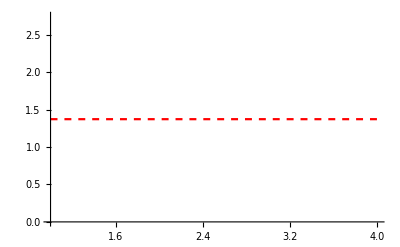
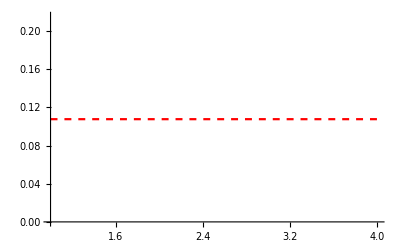
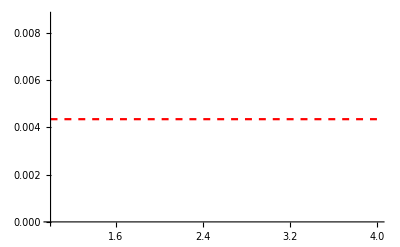
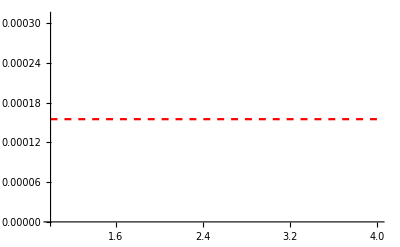

```mathematica
reference=Table[Plot[opeFreeRen[4][[i]],{x,1,4},PlotStyle->{Dashed,Red}],{i,1,4}]
```

zscanhighprec.txt

N::precsm: Requested precision 16 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of N::precsm will be suppressed during this calculation.

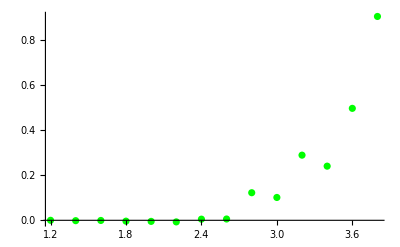
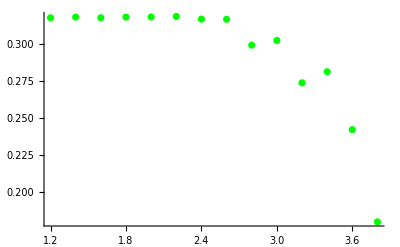
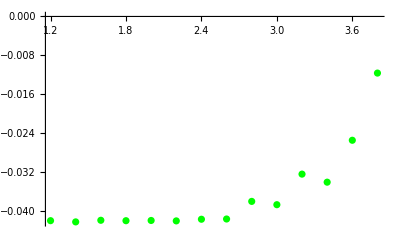
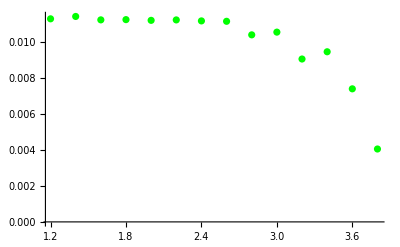

```mathematica
zscanhighprec=Table[checkMetroWScan[1,deltaFree[10],110,123,IntegerPart[10^(i/5)],10^-(6/5),1,1/2000],{i,6,19}];
Export["zscanhighprec.txt",zscan]
ztableshi=Table[ListPlot[{(#/5)&/@Range[6,19],zscanhighprec[[;;,1,1,i]]}//Transpose,PlotStyle->Green],{i,1,4}]
```

```mathematica
Table[Export["zscan-OPE="<>ToString[i]<>".pdf",Show[ztables[[i]],ztableshi[[i]],reference[[i]],PlotRange->All]],{i,1,4}]
```

Part::partw: Part 4 of … does not exist.

Show::gcomb: Could not combine the graphics objects in ….

Part::partw: Part 4 of … does not exist.

Show::gcomb: Could not combine the graphics objects in ….

{zscan-OPE=1.pdf,zscan-OPE=2.pdf,zscan-OPE=3.pdf,zscan-OPE=4.pdf}

```mathematica
nz200=Table[checkMetroWScan[1,deltaFree[7],90,123,200,10^-(6/5),i,j/200000],{i,2,4},{j,-20,20}];
Export["nz200_data_relscan.txt",nz200]
```

nz200_data_relscan.txt

```mathematica
nz1000=Table[checkMetroWScan[1,deltaFree[10],90,123,1000,10^-(6/5),i,j/200000],{i,2,4},{j,-20,20}];
Export["nz1000_data_relscan.txt",nz1000]
```

nz1000_data_relscan.txt

```mathematica
plotsChinz1000=Table[ListPlot[{(#/200000)&/@Range[-20,20],nz1000[[i,;;,1,3]]}//Transpose,PlotRange->All,Joined->True,AxesLabel->{i+1,χ^2},PlotStyle->Green],{i,1,3}];
plotsChinz200=Table[ListPlot[{(#/200000)&/@Range[-20,20],nz200[[i,;;,1,3]]}//Transpose,PlotRange->All,Joined->True,AxesLabel->{i+1,χ^2},PlotStyle->Blue],{i,1,3}];
```

N::precsm: Requested precision 16 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of N::precsm will be suppressed during this calculation.

N::precsm: Requested precision 16 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of N::precsm will be suppressed during this calculation.

```mathematica
Table[Export["plotChiDeltaScan_Nz=200-1000_OpVar="<>ToString[i]<>".pdf",Show[plotsChinz200[[i]],PlotRange->All]],{i,1,3}];
```

```mathematica
plotsnz1000=Table[ListPlot[{(#/200000)&/@Range[-20,20],nz1000[[i,;;,1,1,j]]}//Transpose,PlotRange->All,Joined->True,AxesLabel->{i+1,j},PlotStyle->Green],{i,1,3},{j,2,4}];
```

N::precsm: Requested precision 16 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of N::precsm will be suppressed during this calculation.

```mathematica
plotsnz200=Table[ListPlot[{(#/200000)&/@Range[-20,20],nz200[[i,;;,1,1,j]]}//Transpose,PlotRange->All,Joined->True,AxesLabel->{i+1,j}],{i,1,3},{j,2,4}];
```

N::precsm: Requested precision 16 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of N::precsm will be suppressed during this calculation.

```mathematica
reference=Table[Plot[opeFreeRen[4][[i]],{x,(-20/200000),(20/200000)},PlotStyle->{Dashed,Red}],{i,2,4},{j,2,4}];
```

```mathematica
Table[Export["plotOpeDeltaScan_Nz=200-1000_OpVar="<>ToString[i+1]<>"OPE="<>ToString[j+1]<>".pdf",Show[plotsnz200[[i,j]],plotsnz1000[[i,j]],reference[[j,i]],PlotRange->All]],{i,1,3},{j,1,3}]
```

{{plotOpeDeltaScan_Nz=200-1000_OpVar=2OPE=2.pdf,plotOpeDeltaScan_Nz=200-1000_OpVar=2OPE=3.pdf,plotOpeDeltaScan_Nz=200-1000_OpVar=2OPE=4.pdf},{plotOpeDeltaScan_Nz=200-1000_OpVar=3OPE=2.pdf,plotOpeDeltaScan_Nz=200-1000_OpVar=3OPE=3.pdf,plotOpeDeltaScan_Nz=200-1000_OpVar=3OPE=4.pdf},{plotOpeDeltaScan_Nz=200-1000_OpVar=4OPE=2.pdf,plotOpeDeltaScan_Nz=200-1000_OpVar=4OPE=3.pdf,plotOpeDeltaScan_Nz=200-1000_OpVar=4OPE=4.pdf}}

```mathematica
c=Table[{{nop,2+isigmaz/5,IntegerPart[10^(inz/3)]},checkMetroWeighted[1,deltaFree[nop],110,123,IntegerPart[10^(inz/3)],10^-(2+isigmaz/5)]},{nop,4,10},{isigmaz,1,1},{inz,5,9}];
Print[Dimensions[c]];
Export["scanningOPEsolverhighnz-refinementin_sigmaz-noren.txt",c]
```

{7,1,5,2}

scanningOPEsolverhighnz-refinementin_sigmaz-noren.txt

```mathematica
nz1000[[1,;;,1,2,2]]
```

{41166.6751719415818425435928830977724785985535861002081109870097109379348439490077241554031,39209.7922199784578187696600367848860531141527496880516444598291202032470482740128134800765,37253.5458164499683113326442480547947497282629035936391686098166048317407477034017983535422,35298.0438134571881149539477436302881356340774882623093863815419578059782983426544184243769,33343.4193186858368036307669298371034000992285818319327599172288532711864668232380350083595,31389.8385272564199394268108297949873951062706054659797296568466019903124045537256312182717,29437.5116514400713474301978652090558293118737683807995842648966597708040115316121889269218,27486.7084734199157546802020072465806917437071746872873279936043544486843229083537625269723,25537.78096561387278703515950383703875524049700127080150071563405773112856656582007348777,23591.1970133535865014906540910247688043056786779477512306275401699184675674411439599349321,21647.5921245120765609186814047155625211316490097920087411520172160021514691338562448835464,19707.8513265413050264330235450555222821915449768209538226513328492052163721830205782017085,17773.2438329631159192322821259216943688036917032654904975413830374222480497667196015427422,15845.6544378885007657137172489976586619187720537298815335703826033537946952703539611946179,13928.0024063933489098661884804993193098046798881160687742473886539819327635011016689216874,12025.0487822840630126837274498108693297895305873705862915920452348350555936228957838363384,10145.0750901889368747531610327633454774514182167528925399692119909863486394811494979616107,8303.71270040209081528678918900084314675000327939005704812176227049695736714624511369474885,6533.69946997636871403467992307511054642398355693472378754477040805820293498809290815338986,4912.78368324110337415469626353601516485507852977287896328882757814813918738528931815393281,3645.60438727877210013897172720481364836635708376548616753505571310542611945765169587959999,3186.5866896575883483270232802016563170470789909676899120735123092631058572605442908383221,3837.61594511801347803643696526987608023171800590982958431992344004698156435933130620518511,5197.06244545153963803813484129856136258878689810756898446350899139461846824603283991069421,6855.72483184611139578376410388521932870042624582332105712305016126167463875811120525049293,8643.02917662560750026528149088935628839840742512908455147541314388125651424274308677278602,10493.453753598186887287570549743103137555015496356534963572562232701796724191658186898213,12378.7301629459711032046777495563868698483812034835233961340618997006413630362120898077183,14285.0713032201631788237408448663935239390243113363278362965563546024637952190531414999552,16205.0491896556647379895260278276863082788107785430685087066464633561328162744775199514282,18134.3368844499658942598805707819549485342406021067660690158242331390956848945185265975566,20070.2533523276523913443289603884414976292471738361083072150978293769828965683840931259496,22011.0528574640515642049652878999823801909128191094331118954847103770990727415855962354075,23955.5515806607727962178930527591301845588264973562601937568320858413305009025426670776685,25902.9191991843129442187571156421128948273839550535926914444323469043517900089374965564935,27852.5565237153318738485599380494026527727535883990999510630089533675943558544189726818646,29804.0205279807930051198346679948928359873408564728505310335681309139412362827803079484759,31756.9767092874040815281603608365778068897865084753418574513621647343546414793869849273313,33711.1678476439831741255288000520219890103798247651168197569960608131727107890619117110007,35666.3929483567181584233539963491947014202188570331623854590683658241202874756113268574071,37622.492701842283223215306407009457258540342523027300094367140629885210406441812304437988}

```mathematica
Table[nops=Table[((c[[i,isigmaz,inz-8,2,1,1]]-opeFreeRen[i+3])/opeFreeRen[i+3])//Abs//Log,{i,1,7}];
Export["plot_error_vsnops_sigmaz=e-"<>ToString[isigmaz]<>"nZ="<>ToString[IntegerPart[10^(inz/3)]]<>".pdf",ListPlot[nops,Joined->True,PlotRange->All,PlotLegends->Range[4,10]]],{isigmaz,1,1},{inz,5,1}];
```

```mathematica
.
```

```mathematica
opeFreeRen[10]//N[#,16]&
```

N::precsm: Requested precision 16 is smaller than $MinPrecision. Using $MinPrecision instead.

{1.37258300203047921917298041264483074288524999396883082917312419214828034460628737839379945,0.107746856178060456144838513517536002623332770424210722824924600506165496586821983421282071,0.00434985779123783926385603548801203405620234583718724331763004088806303771681978597502884918,0.000155209524714349057538825346929606959682028255955146402887197662305490799933856487023069281,5.24842547270864475024379495515661529009771740440326633542311031384208594731947696588461679×10^-6,1.72197273888787647074919783508837749408166080919427809228549793816188495609121356403851427×10^-7,5.54128289124616071504541353827163978026436499179924916693432294861213243480547242119956502×10^-9,1.75928089823202471701257863969421911646375988543557721073551777235318710187370040781388197×10^-10,5.53024010329181558303406311048481483425431404936258872893030729204417552224804971382648872×10^-12,1.72520488603068371342306570847829587463522257771554951425448620915745781398461633551323129×10^-13}

```mathematica
(*{{5,2,IntegerPart[10^(5/2)]},checkMetroWeighted[1,deltaFree[5],90,123,IntegerPart[10^(5/2)],10^(-2)]}*)
```

```mathematica
{a[[7,2,1,2,1]],a[[7,2,1,1]]}
```

{{{1.37257970651260166302466383575183274085465765330150071169283778633436034309969250130633089,0.107747361272111337405386537139064438674560790098177394637568833924946355787988059722407516,0.00434974517555402600687982812360566294989987254139640543164314876667128251101161848112151455,0.000155237072557288729831721340340089082343156928005776544907928144404284892139218521966947662,5.24193234262788341915153253604505105941935728989643853536264081507562560255419768519667433×10^-6,1.73571604121340870707185850667045609577038884821233177185124548763208779883500066810691658×10^-7,5.29464689979747413477036096335278423092225273014452959540849810452872144656506014096929695×10^-9,2.11173099707007706742880935973043068000090489419640178578267921818373154206326159339647918×10^-10,1.85934804817775880571145023064617751919278703222469724040573266490151919144453422236106152×10^-12,4.08338341939276916829200311477766089318008459914519219872746972659280136205315957232970014×10^-13},4.99733829764169515334039671565362225121250328853066577650992640055881717691293237259958346×10^-50},{10,2,46}}

```mathematica
renomFactor[2]//N
```

1.45711

```mathematica
2/renomFactor[2]//N
```

1.37258

```mathematica
a[[7,2,1,2,1]]
```

{{1.37257970651260166302466383575183274085465765330150071169283778633436034309969250130633089,0.107747361272111337405386537139064438674560790098177394637568833924946355787988059722407516,0.00434974517555402600687982812360566294989987254139640543164314876667128251101161848112151455,0.000155237072557288729831721340340089082343156928005776544907928144404284892139218521966947662,5.24193234262788341915153253604505105941935728989643853536264081507562560255419768519667433×10^-6,1.73571604121340870707185850667045609577038884821233177185124548763208779883500066810691658×10^-7,5.29464689979747413477036096335278423092225273014452959540849810452872144656506014096929695×10^-9,2.11173099707007706742880935973043068000090489419640178578267921818373154206326159339647918×10^-10,1.85934804817775880571145023064617751919278703222469724040573266490151919144453422236106152×10^-12,4.08338341939276916829200311477766089318008459914519219872746972659280136205315957232970014×10^-13},4.99733829764169515334039671565362225121250328853066577650992640055881717691293237259958346×10^-50}

```mathematica
Table[nops=Table[((a[[i,j,2,2,1,1]]-opeFreeRen[i+3])/opeFreeRen[i+3])//Abs//Log,{i,1,7}];
Export["plot_error_vsnops_sigmaz=e-"<>ToString[j]<>".pdf",ListPlot[nops,Joined->True,PlotRange->All,PlotLegends->Range[4,10]]],{j,1,4}]
```

N::precsm: Requested precision 16 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of N::precsm will be suppressed during this calculation.

{plot_error_vsnops_sigmaz=e-1.pdf,plot_error_vsnops_sigmaz=e-2.pdf,plot_error_vsnops_sigmaz=e-3.pdf,plot_error_vsnops_sigmaz=e-4.pdf}

N::precsm: Requested precision 16 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of N::precsm will be suppressed during this calculation.

N::precsm: Requested precision 16 is smaller than $MinPrecision. Using $MinPrecision instead.

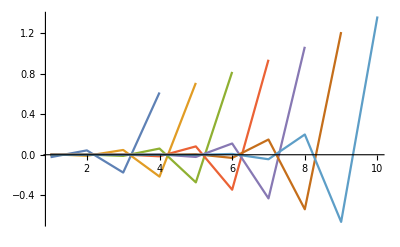

```mathematica
Table[nops=Table[((a[[i,isigmaz,inz-8,2,1,1]]-opeFreeRen[i+3])/opeFreeRen[i+3])//Abs//Log,{i,1,7}];
Export["plot_error_vsnops_sigmaz=e-"<>ToString[isigmaz]<>"nZ="<>ToString[IntegerPart[10^(inz/3)]]<>".pdf",ListPlot[nops,Joined->True,PlotRange->All,PlotLegends->Range[4,10]]],{isigmaz,1,4},{inz,9,12}];
```

```mathematica
a[[7,2,3,2,1,1]]
```

{1.3725797037512316326788853387918766508753487875513983596256476422009818740310230155311199189450669016778598017,0.10774736169354698837920603471367372784676778243224752192707941120166914420440781384009160166355479963752398871,0.0043497450829344342291935399344754481098459039767540833623473409826807556597738136825918462393316540320321653389,0.00015523709454328269027726628597491357013278921221883939774958189524877195235434346670281963112194121124958562632,5.2419274195655273683796200906881107673939439728126042685708263631274736732010807952392237673278054485106775736×10^-6,1.7357256658058836461146259131294885541616517209382910942238382481498294317281993823737659000529478874041780862×10^-7,5.2944933609296274110343770525736139815177353626793563013660960047455625790236009103843527632666731225038019525×10^-9,2.1119153350218394807234768419737178023123649556396398226568462102602620094134034253293956319678005373527708693×10^-10,1.8578830717959333346863058883825284276850835638703879586119351830665383081911995489959570060550667465441261641×10^-12,4.0839573598870975608259852182476620052589535829303378450266812439376913169100088066102721240872301822437722183×10^-13}

```mathematica
data =Get["scanningOPEsolver.txt"];
chi=data[[]];
```

```mathematica
Dimensions[data]
```

{4,5,2}

```mathematica
b//Dimensions
```

{7,4,8,2}

```mathematica
logNz=(#/3)&/@Range[5,12]
```

{5/3,2,7/3,8/3,3,10/3,11/3,4}

N::precsm: Requested precision 16 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of N::precsm will be suppressed during this calculation.

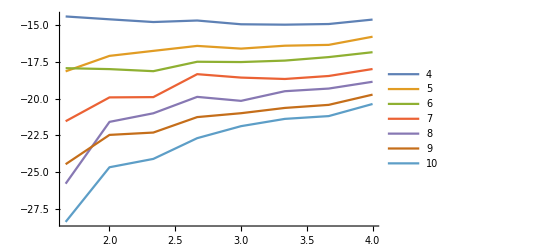
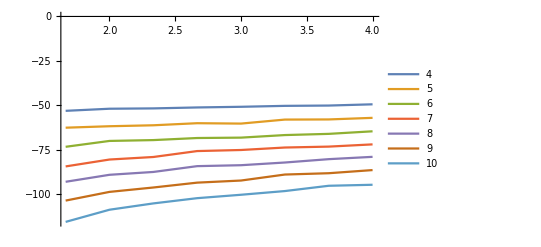
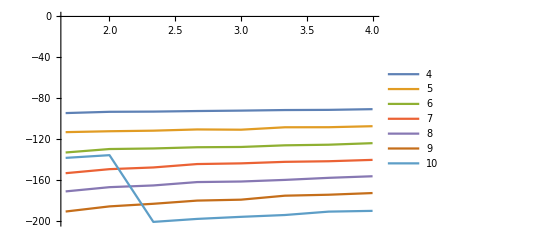
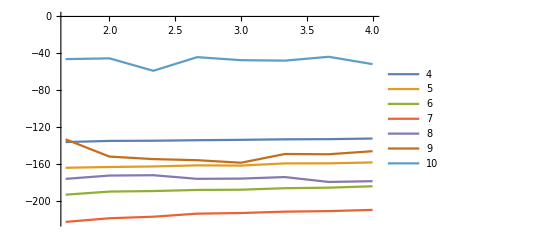

```mathematica
plots=ListPlot[Table[({logNz,b[[i,#,;;,2,1,2]]//Log}//Transpose),{i,1,7}],Joined->True,PlotRange->All,PlotLegends->Range[4,10]]&/@Range[1,4]
```

```mathematica
plots[[1]]
```

-Graphics-

```mathematica
Table[Export["plot_chivsNz_sigmaz=e-"<>ToString[i]<>".pdf",plots[[i]]],{i,1,4}]
```

{plot_chivsNz_sigmaz=e-1.pdf,plot_chivsNz_sigmaz=e-2.pdf,plot_chivsNz_sigmaz=e-3.pdf,plot_chivsNz_sigmaz=e-4.pdf}

```mathematica
#
```

N::precsm: Requested precision 16 is smaller than $MinPrecision. Using $MinPrecision instead.

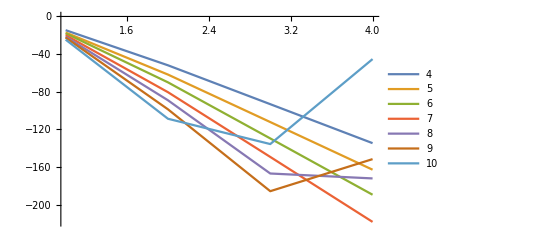

```mathematica
ListPlot[b[[;;,;;,2,2,1,2]]//Log,Joined->True,PlotRange->All,PlotLegends->Range[4,10]]
```